# Trend duration analysis

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

SignRatio[returns_]:= N[Count[Map[Sign,returns],1]/Length[returns]];
PriceChangeRatio[returns_]:=Total[Select[returns,Positive]]/Total[Abs[returns]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

DatedTrendDuration[datedprices]
DatedTrendDuration[dates, prices]
calculates TrendDuration with date info.

## Database

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","DJI_NASDAQ_MXX_NIKKEI_datasetV2.wdx"}];
(*path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];*)
database = Import[path];
database[[All,"Name"]] = {"DJIA","NASDAQ Composite","IPC","Nikkei 225"};
```

Date fixer: There are no dates in the original dataset, this generates the intermediate dates.

```mathematica
GenerateDaysBetween[firstDate_DateObject,lastDate_DateObject,length_]:=Block[{dayRange,dayCount,ratio},
dayRange = DayRange[firstDate,lastDate];
dayCount = DayCount[firstDate,lastDate];
ratio = dayCount/length;
Table[Part[dayRange,Floor[i*ratio]],{i,length}]
];
AddToDataset[database,"Dates",GenerateDaysBetween[DateObject[#1],DateObject[#2],Length[#3]]&,{"FirstDate","LastDate","Prices"}];
```

```mathematica
orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

## Trend example

Figure. 1

```mathematica
smallSample = Take[database[[2]]["Prices"],50];
smallSampleInTime = Transpose[{Range[50],smallSample}];
smallTr = DatedTrendReturns[Range[50],smallSample];
pricesInTr = smallSampleInTime[[smallTr[[All,1]]]];
```

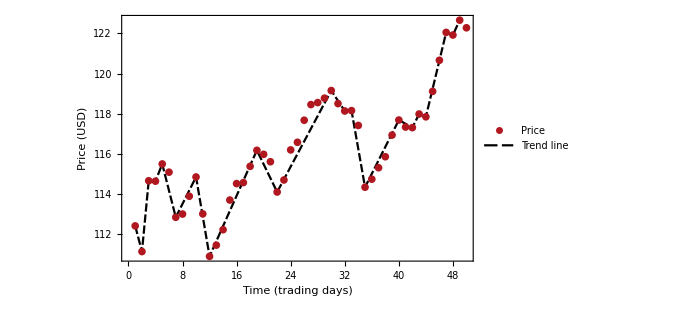

```mathematica
figure = ListPlot[
{smallSampleInTime,pricesInTr},
Joined->{False, True},
ImageSize->500,
PlotTheme->"Monochrome",
FrameLabel->{Style["Time (trading days)",15],Style["Price (USD)",15]},
Frame->True,BaseStyle->FontSize->14,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->colors,
PlotLegends->Placed[LineLegend[{"Price", "Trend line"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}]
]
```

## Example of trend duration plot

```mathematica
market = First[database];
durations = TrendDuration[market["Prices"]];
```

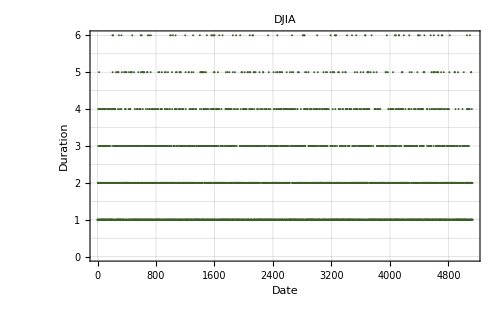

```mathematica
ListPlot[
durations,
PlotTheme->"Monochrome", 
Frame->True,
FrameLabel->{Style["Date",15], Style["Duration",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True
]
```

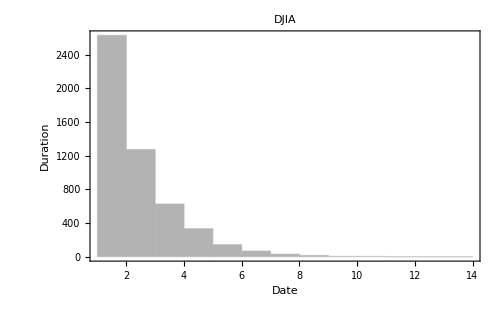

```mathematica
Histogram[
durations,
PlotTheme->"Monochrome", 
Frame->True,
FrameLabel->{Style["Date",15], Style["Duration",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
```

## Efficient market model

```mathematica
market = First[database];
```

```mathematica
Take[market["Prices"],10]
```

{811.85,792.45,827.79,816.96,823.11,814.88,800.07,807.61,803.97,807.09}

```mathematica
DivReturns[prices_]:=Drop[prices,1]/Drop[prices,-1];
```

```mathematica
Qi = DivReturns[market["Prices"]];
```

```mathematica
FindDistribution[Qi]
```

MixtureDistribution[{0.446978,0.553022},{NormalDistribution[1.06001,0.0299607],NormalDistribution[0.951386,0.0364293]}]

```mathematica
param = FindDistributionParameters[Qi,LogNormalDistribution[μ,σ]]
```

{μ→0.000338089,σ→0.0107221}

```mathematica
fitted = LogNormalDistribution[μ,σ]/.param
```

LogNormalDistribution[0.000338089,0.0107221]

```mathematica
DistributionFitTest[Qi,fitted]
```

0.

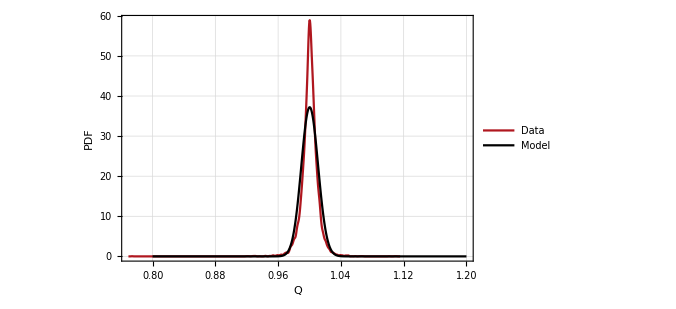

```mathematica
Show[
SmoothHistogram[Qi,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Q",15], Style["PDF",15]},
BaseStyle->FontSize->13,
ImageSize->500,
PlotStyle->First[colors],
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True,
PlotLegends->{"Data"}
],
Plot[PDF[fitted,x],{x,0.8,1.2},
PlotRange->All,
PlotStyle->Black,
PlotLegends->{"Model"}
]
]
```

```mathematica
riskFreeDataset = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","RiskFreeReturn","RiskFreeRet_Database.wdx"}]];
```

Fuente: https://mba.tuck.dartmouth.edu/pages/faculty/ken.french/data_library.html

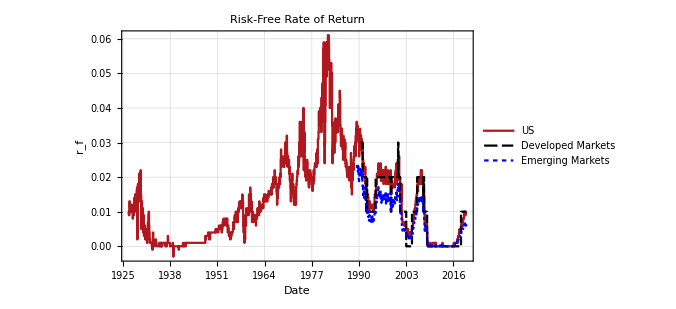

```mathematica
DateListPlot[
riskFreeDataset[[All,"DateReturns"]],
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["r_f",15]},
BaseStyle->FontSize->13,
PlotLabel->"Risk-Free Rate of Return",
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True,
PlotLegends->{"US","Developed Markets","Emerging Markets"}
]
```

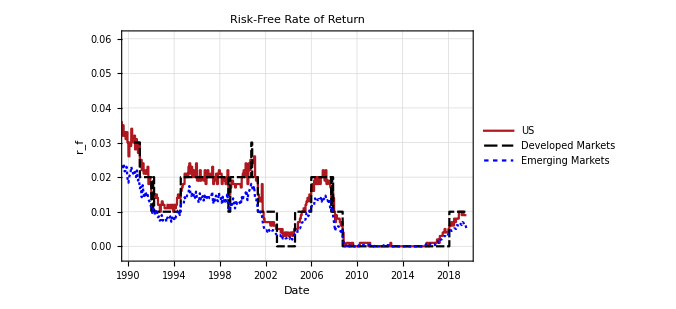

```mathematica
DateListPlot[
riskFreeDataset[[All,"DateReturns"]],
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["r_f",15]},
BaseStyle->FontSize->13,
PlotLabel->"Risk-Free Rate of Return",
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True,
PlotLegends->{"US","Developed Markets","Emerging Markets"},
PlotRange->{{DateObject[{1990,1},"Month","Gregorian",-5.],DateObject[{2019,8},"Month","Gregorian",-5.]},Automatic}
]
```

```mathematica
Min[Flatten[riskFreeDataset[[All,"DateReturns"]][[All,All,1]]]]
```

```mathematica
Table[Min[riskFreeDataset[[All,"DateReturns"]][[i]][[All,1]]],{i,1,3}]
```

{Day: Thu 1 Jul 1926,Day: Mon 2 Jul 1990,Month: Jul 1989}

```mathematica
GetRfRate[date_,type_]:=Block[{usRiskFreeData,devRiskFreeData,emRiskFreeData,correctedDate,result},
usRiskFreeData = riskFreeDataset[[1]];
devRiskFreeData = riskFreeDataset[[2]];
emRiskFreeData = riskFreeDataset[[3]];

correctedDate = date;
If[DayName[date]==Saturday,correctedDate = DatePlus[date,2]];
If[DayName[date]==Sunday,correctedDate = DatePlus[date,1]];

If[correctedDate<DateObject[{1990,7,2},"Day","Gregorian",-5.],correctedDate = DateObject[{1990,7,2},"Day","Gregorian",-5.]];
If[correctedDate>DateObject[{2019,7,31},"Day","Gregorian",-5.],correctedDate =DateObject[{2019,7,31},"Day","Gregorian",-5.]];

If[type == "US",
result = FirstCase[usRiskFreeData["DateReturns"],{correctedDate,x_}:>x]
];
If[type == "Developed",
result = FirstCase[devRiskFreeData["DateReturns"],{correctedDate,x_}:>x]
];
If[type == "Emerging",
correctedDate = DateObject[Take[DateList[correctedDate],2]];
result = FirstCase[emRiskFreeData["DateReturns"],{correctedDate,x_}:>x]
];

If[result ===Missing["NotFound"],
result = GetRfRate[DatePlus[correctedDate,5],type]
];

Return[result];
];
Estimateσ[divReturns_]:=Block[{μ,σ},
σ/.FindDistributionParameters[divReturns,LogNormalDistribution[μ,σ]]
];
Estimateμ[divReturns_]:=Block[{μ,σ},
μ/.FindDistributionParameters[divReturns,LogNormalDistribution[μ,σ]]
];
CalculateQ[{σ_,rf_}]:=1/2+1/2 Erf[σ/(2 √2)-Log[1+rf]/(σ √2)];
CalculateQv2[{μ_,rf_}]:=1/2+1/2 Erf[-μ/(√(4( Log[1+rf]- μ)))];
```

### Estimación de q a partir de la desviación estándar

```mathematica
EstimateQFromStdDev[market_,type_]:=Block[{datedPrices,parts,rfs,σs,qs},
datedPrices =Transpose[{market["Dates"],market["Prices"]}];
parts = Partition[datedPrices,504,10];
rfs = Map[GetRfRate[First[Last[#]],type]&,parts];
σs = Map[Estimateσ[DivReturns[#[[All,2]]]]&,parts];
qs = Map[CalculateQ,Transpose[{σs,rfs}]];

ListLinePlot[qs,
Frame->True,
PlotRange->{Automatic,{0,0.6}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["q",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
PlotStyle->First[colors],
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True
]
];
```

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

ReplaceAll::reps: {FindDistributionParameters[{0.945963,0.97687,0.951584,1.07156,1.00199,0.986417,1.02276,0.985823,1.00901,0.996338,0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,«14»,0.9982,0.98687,0.992873,0.964525,0.99747,0.975783,0.99889,1.00219,1.00455,0.995551,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,«453»},«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

ReplaceAll::reps: {FindDistributionParameters[{0.945963,0.97687,0.951584,1.07156,1.00199,0.986417,1.02276,0.985823,1.00901,0.996338,0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,«14»,0.9982,0.98687,0.992873,0.964525,0.99747,0.975783,0.99889,1.00219,1.00455,0.995551,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,«453»},«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

General::stop: Further output of FindDistributionParameters::ntsprt will be suppressed during this calculation.

ReplaceAll::reps: {FindDistributionParameters[{0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,0.992421,0.991602,1.01263,1.00513,1.01741,0.99323,0.991668,0.997757,0.987508,1.01936,«14»,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,1.02704,1.01203,0.992421,0.995067,0.996382,0.963885,0.968879,0.997482,1.00679,1.02153,«453»},«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

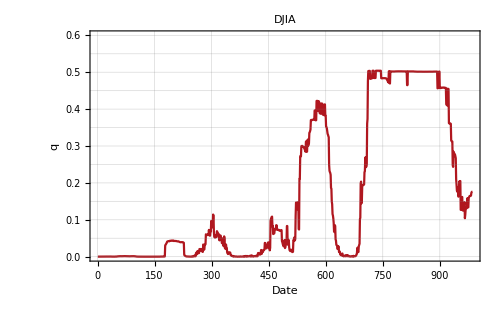
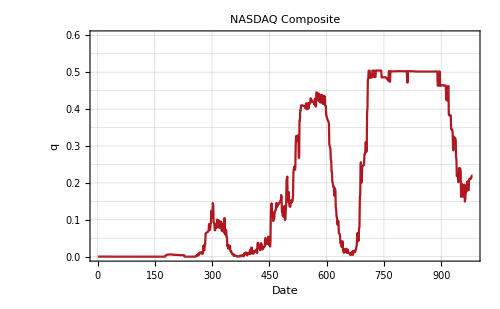
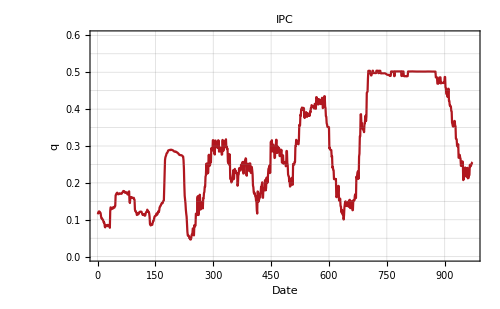
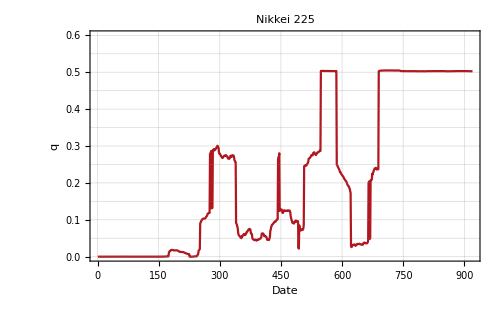

```mathematica
MapThread[EstimateQFromStdDev,{database,{"US","US","Emerging","Developed"}}]
```

#### Individual

```mathematica
datedPrices =Transpose[{First[database]["Dates"],First[database]["Prices"]}];
parts = Partition[datedPrices,504,10];
rfs = Map[GetRfRate[First[Last[#]],"US"]&,parts];
σs = Map[Estimateσ[DivReturns[#[[All,2]]]]&,parts];
qs = Map[CalculateQ,Transpose[{σs,rfs}]];
```

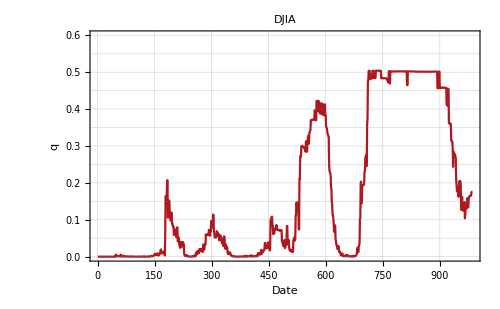

```mathematica
ListLinePlot[qs,
Frame->True,
PlotRange->{Automatic,{0,0.6}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["q",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
PlotStyle->First[colors],
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True
]
```

### Estimación de q a partir de la media

```mathematica
EstimateQFromMean[market_,type_]:=Block[{datedPrices,parts,rfs,μs,qs2},
datedPrices =Transpose[{market["Dates"],market["Prices"]}];
parts = Partition[datedPrices,504,10];
rfs = Map[GetRfRate[First[Last[#]],type]&,parts];
μs = Map[Estimateμ[DivReturns[#[[All,2]]]]&,parts];
qs2 = Map[CalculateQv2,Transpose[{μs,rfs}]];

ListLinePlot[qs2,
Frame->True,
PlotRange->{Automatic,{0,0.6}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["q",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
PlotStyle->First[colors],
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True
]
];
```

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

ReplaceAll::reps: {FindDistributionParameters[{0.945963,0.97687,0.951584,1.07156,1.00199,0.986417,1.02276,0.985823,1.00901,0.996338,0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,«14»,0.9982,0.98687,0.992873,0.964525,0.99747,0.975783,0.99889,1.00219,1.00455,0.995551,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,«453»},«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

ReplaceAll::reps: {FindDistributionParameters[{0.945963,0.97687,0.951584,1.07156,1.00199,0.986417,1.02276,0.985823,1.00901,0.996338,0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,«14»,0.9982,0.98687,0.992873,0.964525,0.99747,0.975783,0.99889,1.00219,1.00455,0.995551,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,«453»},«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution LogNormalDistribution[μ,σ].

General::stop: Further output of FindDistributionParameters::ntsprt will be suppressed during this calculation.

ReplaceAll::reps: {FindDistributionParameters[{0.991511,1.01411,1.00298,0.990014,1.00367,1.0411,1.01276,1.00322,0.993919,0.992421,0.991602,1.01263,1.00513,1.01741,0.99323,0.991668,0.997757,0.987508,1.01936,«14»,1.01128,1.0284,1.03234,0.996273,0.966045,1.03677,1.0019,1.02704,1.01203,0.992421,0.995067,0.996382,0.963885,0.968879,0.997482,1.00679,1.02153,«453»},«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

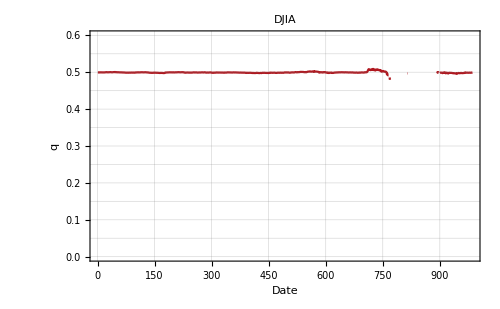
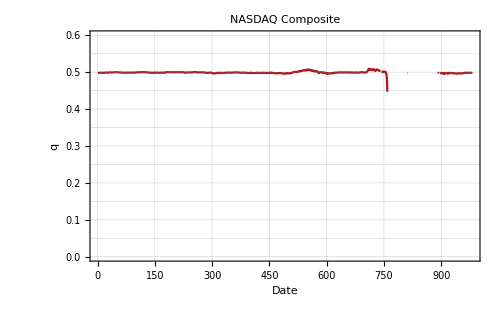
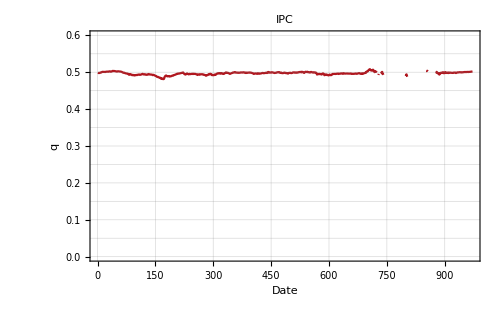
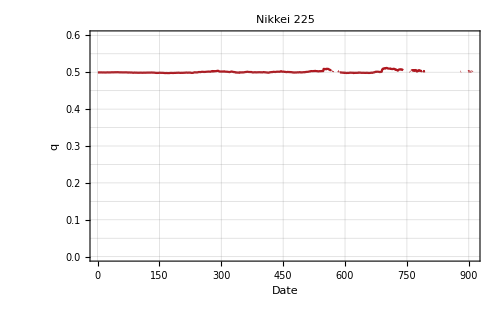

```mathematica
MapThread[EstimateQFromMean,{database,{"US","US","Emerging","Developed"}}]
```

#### Individual

```mathematica
μs = Map[Estimateμ[DivReturns[#[[All,2]]]]&,parts];
qs2 = Map[CalculateQv2,Transpose[{μs,rfs}]];
```

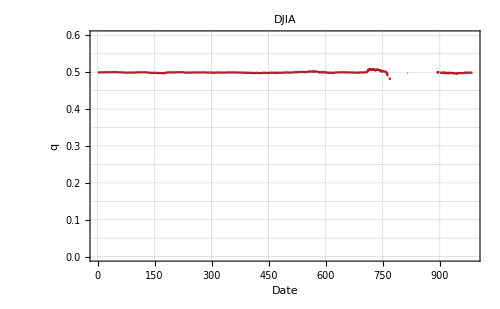

```mathematica
ListLinePlot[qs2,
Frame->True,
PlotRange->{Automatic,{0,0.6}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["q",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
PlotStyle->First[colors],
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True
]
```

## p-values

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
FQ1[rf_,σ_]:=1/2+ 1/2 Erf[σ/(2 √2)-Log[1+rf]/(σ √2)];
FQ1v2[μ_,rf_]:=1/2+1/2 Erf[-μ/(√(4( Log[1+rf]- μ)))];
```

```mathematica
Plot3D[{FQ1[rf,σ],0.5},{rf,0,0.04},{σ,0,0.3},
AxesLabel->{"r_f","σ","q"},
PlotStyle->{Opacity[1],Opacity[0.4]},
PlotLegends->{"F_Q(1)","q=0.5"},BoxStyle->{Black},LabelStyle->Black
]
```

-Graphics3D-

```mathematica
Plot3D[{FQ1v2[μ,rf],0.5},{rf,0.001,0.04},{μ,-0.001,0.001},
AxesLabel->{"r_f","μ","q"},
PlotStyle->{Opacity[1],Opacity[0.4]},
PlotLegends->{"F_Q(1)","q=0.5"},BoxStyle->{Black},LabelStyle->Black
]
```

-Graphics3D-

Anderson-Darling test for trend durations assuming that the underlying distribution is a GeometricDistribution[p] with p = 0.5.

Figure 4.

```mathematica
CalculateADPiValuesSpecified[dates_,prices_,window_, skip_ :1]:=Module[{datePricesPart,trendDurationParts,ad,lastDates},
datePricesPart = Partition[Transpose[{dates,prices}],window,skip];
trendDurationParts = Map[Apply[DatedTrendDuration,Transpose[#]]&,datePricesPart];
ad = ParallelMap[Quiet[AndersonDarlingTest[#-1,GeometricDistribution[0.5]]] &,trendDurationParts[[All,All,2]]];
lastDates = Map[Last,trendDurationParts[[All,All,1]]];
Return[Transpose[{lastDates,ad}]];
];
```

```mathematica
ClosestDate[list_,date_]:=First[MinimalBy[list,Abs[QuantityMagnitude[DateDifference[First[#],date]]]&]];
FixZeros[{n_,m_}]:=If[m==0,{n,10^-6},{n,m}];

PlotADValues[market_]:=Block[{legend,uppList,plotData,firstDate,lastDate},
If[market["Name"] == "NASDAQ Composite",
legend = Placed[LineLegend[{None,"α = 0.1","α = 0.05","α = 0.01"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}];
,
legend = None
];

{firstDate,lastDate} = {First[First[market["ADValuesSpecified"]]],First[Last[market["ADValuesSpecified"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];

plotData = Join[{market["ADValuesSpecified"]},uppList];

DateListLogPlot[
plotData,
PlotRange->{Automatic,{10^-6,1}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["π-Value",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
Joined->{True,True,True,True,False},
PlotStyle->colors,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->legend,
FrameTicks->True
]
];
```

Points below α values indicate the rejection of the null hypothesis D \[Distributed] GeometricDistribution[0.5]

```mathematica
AddToDataset[database,"ADValuesSpecified",CalculateADPiValuesSpecified[#1,#2,504]&,{"Dates","Prices"}];
```

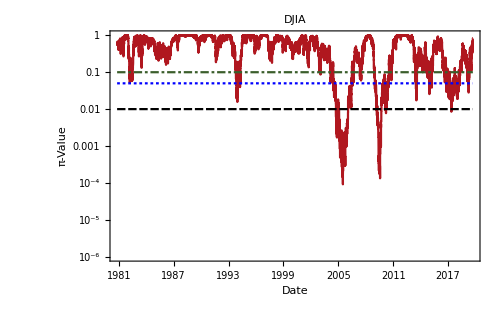
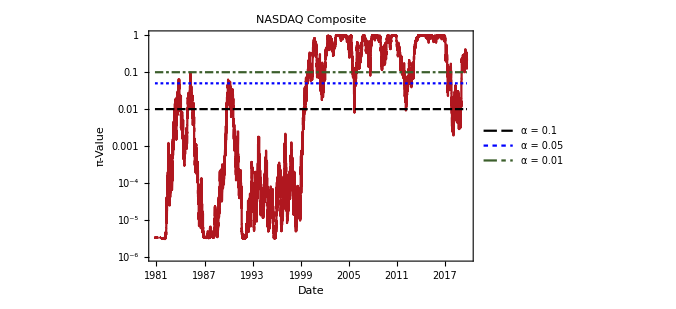
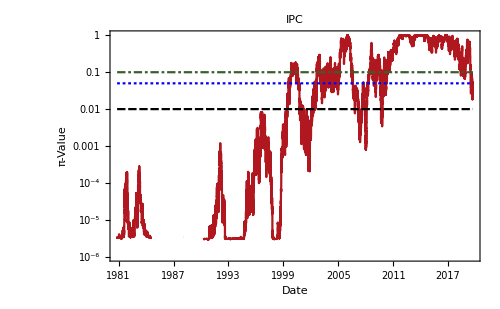
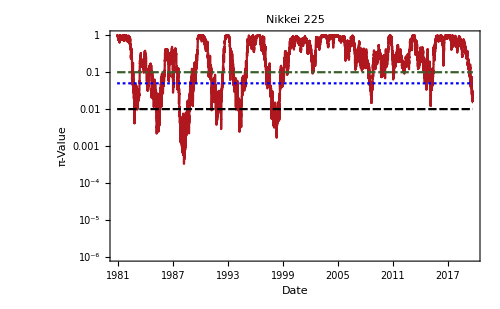

```mathematica
Map[PlotADValues,database]
```

```mathematica
piVs = Map[CalculateADPiValuesSpecified[#["Dates"],#["Prices"],504,10]&,database];
```

```mathematica
notGeometricDates = Table[Select[piV,Last[#]<0.05&][[All,1]],{piV,piVs}];
```

```mathematica
TimelinePlot[notGeometricDates,Frame->True,PlotLegends->database[[All,"Name"]],PerformanceGoal->"Speed"]
```

```mathematica
MDLMeasureP[sample_]:=N[Length[sample]/Total[sample]];
F0[k_,p_]:=CDF[GeometricDistribution[p],k-1];
Fn[k_,empirical_]:=N[CDF[empirical,k]];
p0[k_,p_]:=F0[k,p]-F0[k-1,p];

AndersonDarlingGeometric[sample_]:=Block[{empiricalD,mdlP},
empiricalD = EmpiricalDistribution[sample];
mdlP = MDLMeasureP[sample];
Length[sample]*Sum[((Fn[k,empiricalD]-F0[k,mdlP])^2 p0[k,mdlP])/(F0[k,mdlP](1-F0[k,mdlP])),{k,1,Max[sample]}]
];
ReplicateSample[sample_,replications_]:=Block[{n,mdlP},
n = Length[sample];
mdlP = MDLMeasureP[sample];

Table[RandomVariate[GeometricDistribution[mdlP],n]+1,replications]
];
ADStatistic[sample_,repetitions_]:=Sort[Map[AndersonDarlingGeometric,ReplicateSample[sample,repetitions]]];
ADStatisticFamilyPValue[sample_,repetitions_ :1000]:=Block[{adStatistic},
adStatistic = Sort[Map[AndersonDarlingGeometric,ReplicateSample[sample,repetitions]]];
CDF[EmpiricalDistribution[adStatistic],AndersonDarlingGeometric[sample]]
];
```

```mathematica
market = First[database];
```

```mathematica
sample = Take[TrendDuration[market["Prices"]],504];
```

```mathematica
MDLMeasureP[sample]
```

0.502994

```mathematica
adStatistic = Sort[Map[AndersonDarlingGeometric,ReplicateSample[sample,10000]]];
```

```mathematica
measuredAD = AndersonDarlingGeometric[sample]
```

0.459565

```mathematica
plt1 = SmoothHistogram[
adStatistic,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["OverHat[A_n]",15], Style["PDF",15]},
BaseStyle->FontSize->13,
ImageSize->500,
PlotStyle->First[colors],
FrameTicks->True,
GridLines->{{measuredAD},None}
];
plt2 = SmoothHistogram[
adStatistic,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["OverHat[A_n]",15], Style["PDF",15]},
BaseStyle->FontSize->13,
ImageSize->500,
FrameTicks->True,
PlotRange->{{0,measuredAD},Automatic},
PlotStyle->{Thickness[0],First[colors]},
Filling->Axis,
FillingStyle->LightGray
];
```

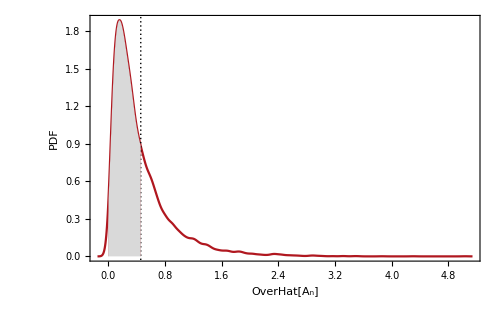

```mathematica
Show[plt1,plt2]
```

```mathematica
ADStatisticFamilyPValue[sample,5000]
```

0.609

```mathematica
CalculateADPiValuesFamily[market_,window_,skip_ :1]:=Module[{datePricesPart,trendDurationParts,ad,lastDates},
datePricesPart = Partition[Transpose[{market["Dates"],market["Prices"]}],window,skip];
trendDurationParts = Map[Apply[DatedTrendDuration,Transpose[#]]&,datePricesPart];
ad = ProgressParallelMap[ADStatisticFamilyPValue,trendDurationParts[[All,All,2]]];
lastDates = Map[Last,trendDurationParts[[All,All,1]]];
Return[Transpose[{lastDates,ad}]];
];
PlotADPiValuesFamily[market_,piV_]:=Block[{legend,firstDate,lastDate,uppList,plotData},
If[market["Name"] == "NASDAQ Composite",
legend = Placed[LineLegend[{None,"α = 0.1","α = 0.05","α = 0.01"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}];
,
legend = None
];

{firstDate,lastDate} = {First[First[piV]],First[Last[piV]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];

plotData = Join[{piV},uppList];

DateListLogPlot[
plotData,
PlotRange->{Automatic,{10^-4,1}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["π-Value",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
Joined->{True,True,True,True,False},
PlotStyle->colors,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->legend,
FrameTicks->True
]
];
```

```mathematica
piVs = Map[CalculateADPiValuesFamily[#,504,10]&,database];
```

$Aborted

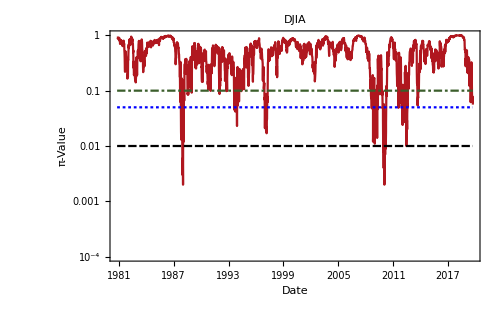
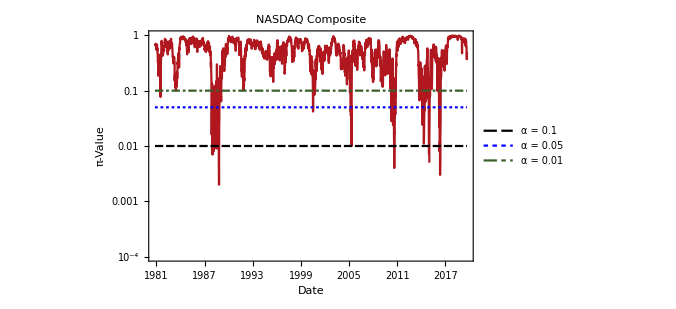
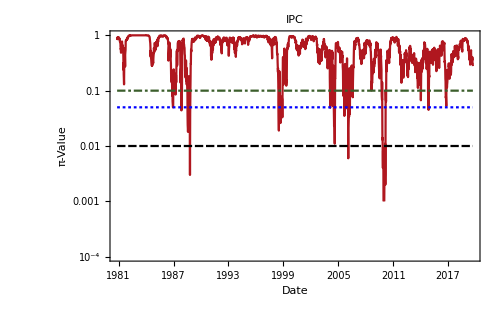
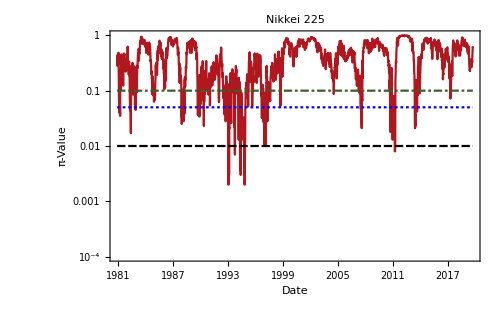

```mathematica
MapThread[PlotADPiValuesFamily,{database,piVs}]
```

```mathematica
notGeometricDates = Table[Select[piV,Last[#]<0.05&][[All,1]],{piV,piVs}];
```

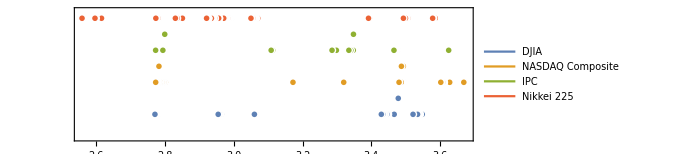

```mathematica
TimelinePlot[notGeometricDates,Frame->True,PlotLegends->database[[All,"Name"]]]
```

## Distribution

Figure 3.

```mathematica
UpwardTrendDuration[prices_] := Module[{splitted,posTrends},
splitted =Split[Sign[SimpleReturns[prices]]];
posTrends = Select[splitted,Apply[Or,Positive[#]]&];
Return[Map[Length,posTrends]];
];
DownwardTrendDuration[prices_] := Module[{splitted,negTrends},
splitted =Split[Sign[SimpleReturns[prices]]];
negTrends = Select[splitted,Apply[Or,Negative[#]]&];
Return[Map[Length,negTrends]];
];
TrendHistogramPoints[prices_,durationFunction_]:=Module[{trendDuration,histogramList},
trendDuration = durationFunction[prices] - 1;
histogramList = Map[{#,Count[trendDuration,#]/Length[trendDuration]}&,DeleteDuplicates[trendDuration]];
Return[histogramList];
];

EstimateP[trendDuration_]:=Module[{p},p/.FindDistributionParameters[trendDuration,GeometricDistribution[p]]];
EstimateP[prices_,durationFunction_]:=EstimateP[durationFunction[prices] - 1];
GoodnessOfFit[prices_,durationFunction_]:=DistributionFitTest[durationFunction[prices]-1,GeometricDistribution[EstimateP[prices,durationFunction]]];

FitTrend[prices_,durationFunction_]:=Module[{trendDuration,p,fittedPts},
trendDuration = durationFunction[prices] - 1;
p = EstimateP[trendDuration];
fittedPts = Table[{k,PDF[GeometricDistribution[p],k]},{k,0,Max[trendDuration]}];
Return[fittedPts];
];

PlotTrendDistribution[trendDatabase_,direction_,color_:Red]:=Block[{fit,histogram,estimatedP,ref,legend},
fit = If[direction=="Upward","UpwardFit","DownwardFit"];
histogram = If[direction=="Upward","UpwardHistogram","DownwardHistogram"];
estimatedP = If[direction=="Upward","UpwardEstimatedP","DownwardEstimatedP"];
ref = GenerateFitted[0.5,Max[trendDatabase[histogram][[All,1]]]];

If[trendDatabase["Name"] == "DJIA",
legend = Placed[
LineLegend[{"Fit","Histogram", "p̂ = 0.5"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
{Left,Bottom}
];
,
legend = None
];

ListLogPlot[
{trendDatabase[fit],trendDatabase[histogram],ref},
Joined->{True,False},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Duration (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->trendDatabase["Name"],
PlotStyle->{color,{PointSize[Large],Black},GrayLevel[0.38]},
Epilog->{Inset[Framed[Text[Style["p̂ = "<>ToString[trendDatabase[estimatedP]],14]],RoundingRadius->1,Background->RGBColor[1,1,1,.8]],Scaled[{0.8,.8}]]},
ImageSize->500,
PlotLegends->legend,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
];
```

Upward trends

```mathematica
AddToDataset[database,"UpwardHistogram",TrendHistogramPoints[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardFit",FitTrend[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardEstimatedP",EstimateP[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardGoodnessFit",GoodnessOfFit[#,UpwardTrendDuration]&,{"Prices"}];
```

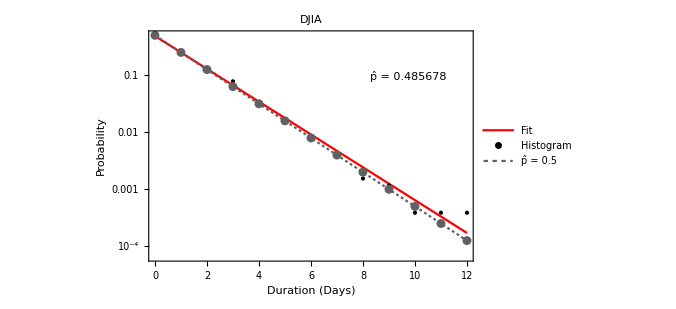
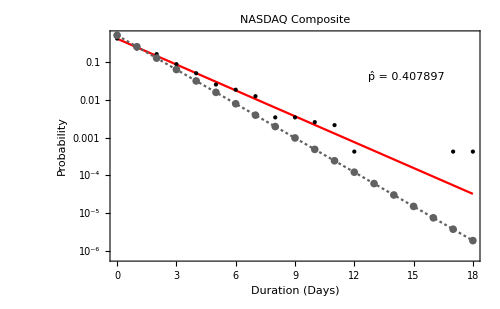
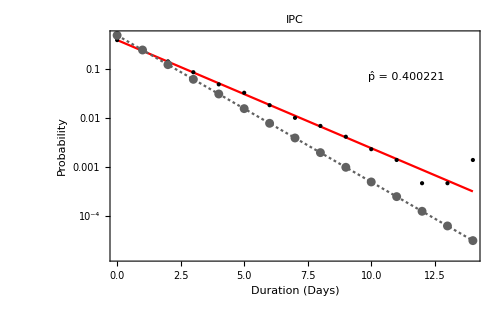
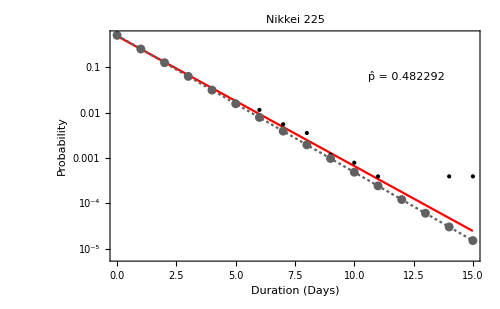

```mathematica
Map[PlotTrendDistribution[#,"Upward",Red]&,database]
```

```mathematica
Dataset@database[[All,{"Name","UpwardGoodnessFit"}]]
```

Dataset[<>]

Downward trends

```mathematica
AddToDataset[database,"DownwardHistogram",TrendHistogramPoints[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardFit",FitTrend[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardEstimatedP",EstimateP[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardGoodnessFit",GoodnessOfFit[#,DownwardTrendDuration]&,{"Prices"}];
```

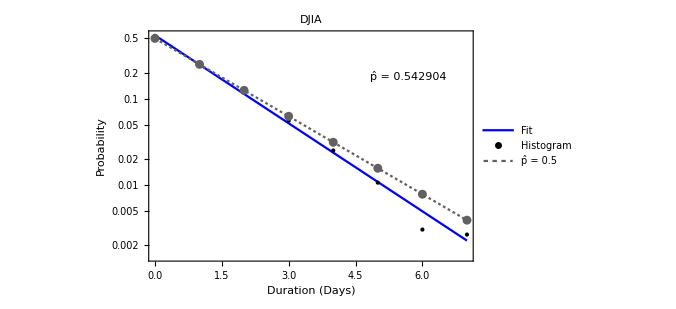
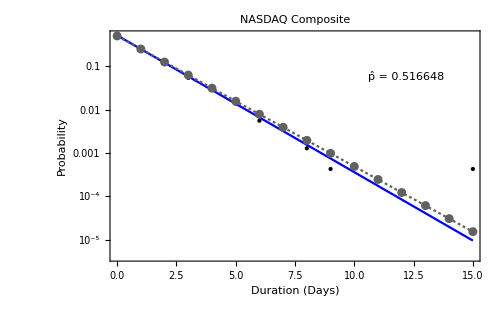
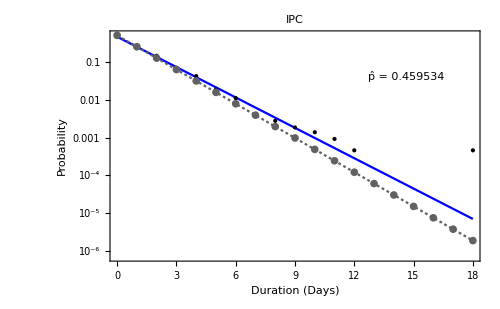
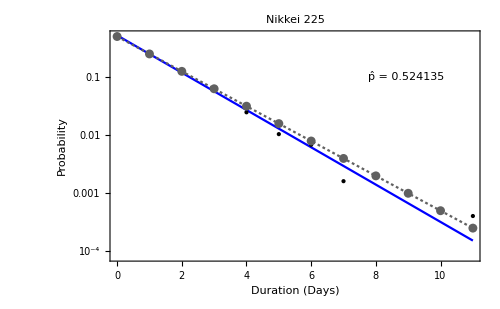

```mathematica
Map[PlotTrendDistribution[#,"Downward",Blue]&,database]
```

```mathematica
Dataset@database[[All,{"Name","DownwardGoodnessFit"}]]
```

Dataset[<>]

Both

```mathematica
PlotTrendDistributionBoth[trendDatabase_]:=Block[{ref,legend},
ref = GenerateFitted[0.5,15];

legend = Placed[
LineLegend[
{
"Upward Fit, p̂ = "<>ToString[trendDatabase["UpwardEstimatedP"]],"Upward Histogram", 
"Downward Fit, p̂ = "<>ToString[trendDatabase["DownwardEstimatedP"]],"Downward Histogram", 
"p̂ = 0.5"
},
LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11
],
{Left,Bottom}
];

ListLogPlot[
{
trendDatabase["UpwardFit"],trendDatabase["UpwardHistogram"],
trendDatabase["DownwardFit"],trendDatabase["DownwardHistogram"],
ref
},
Joined->{True,False,True,False,True},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Duration (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->trendDatabase["Name"],
PlotStyle->{Red,{PointSize[Large],Red},Blue,{PointSize[Large],Blue},GrayLevel[0.38]},
ImageSize->650,
PlotLegends->legend,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->{{0,15},Automatic}
]
]
```

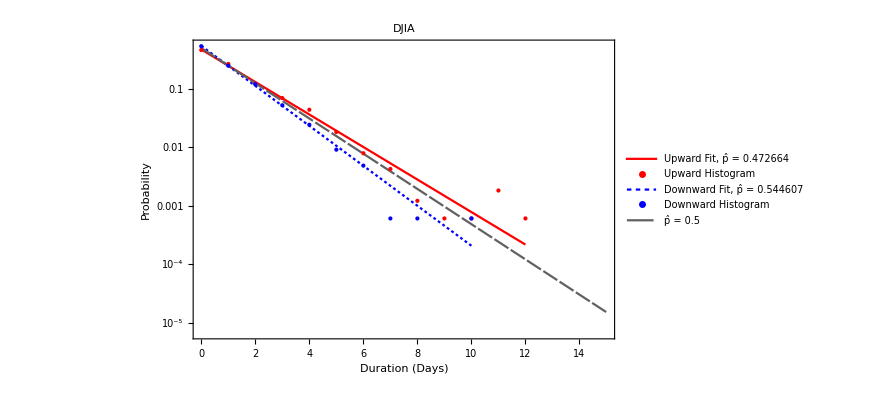
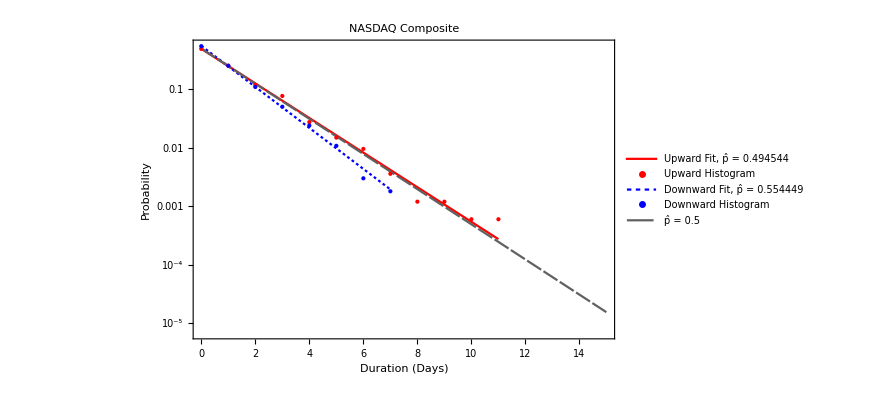
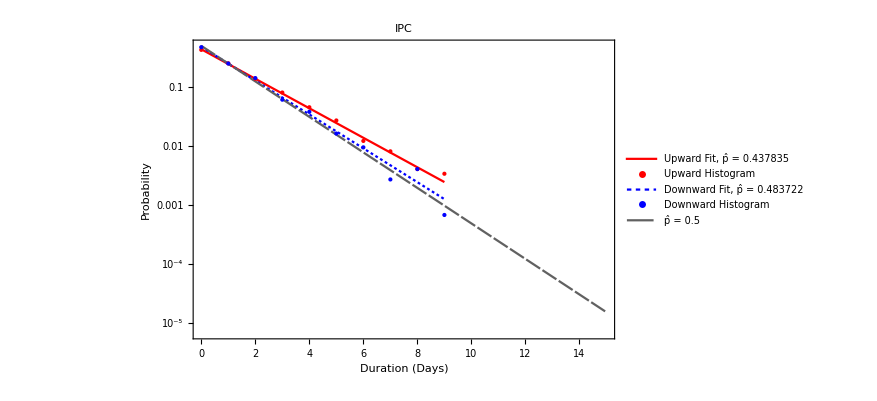
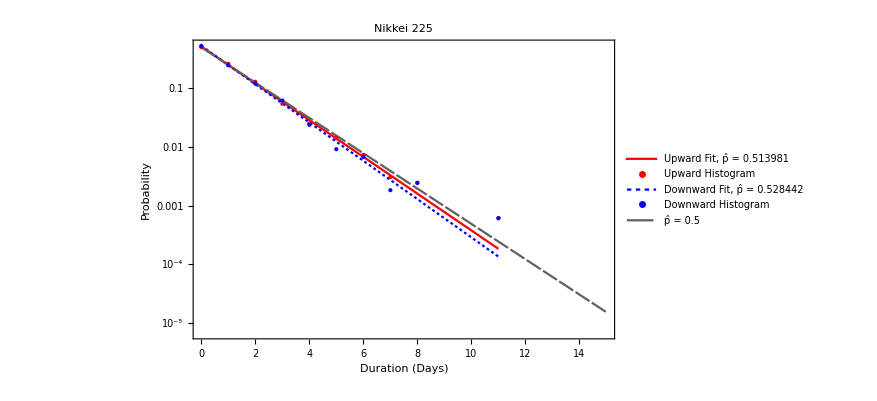

```mathematica
Map[PlotTrendDistributionBoth,database]
```

### Evolution in time

```mathematica
FitTrend2[prices_,durationFunction_,max_]:=Module[{trendDuration,p,fittedPts},
trendDuration = durationFunction[prices] - 1;
p = EstimateP[trendDuration];
fittedPts = Table[{k,PDF[GeometricDistribution[p],k]},{k,0,max}];
Return[fittedPts];
];

PlotTrendDistributionBothTimeEvolution[market_,window_,skip_]:=DynamicModule[{part,legend,data,hs,ref,dates,upwardPoints,upwardFit,upwardEstimatedP,downwardPoints,downwardFit,downwardEstimatedP},
part = Partition[market["Prices"],window,skip];
ref = GenerateFitted[0.5,15];
dates = market["Dates"][[window;;-1;;skip]];

upwardPoints = Map[TrendHistogramPoints[#,UpwardTrendDuration]&,part];
upwardFit = Map[FitTrend2[#,UpwardTrendDuration,15]&,part];
upwardEstimatedP = Map[EstimateP[#,UpwardTrendDuration]&,part];

downwardPoints = Map[TrendHistogramPoints[#,DownwardTrendDuration]&,part];
downwardFit = Map[FitTrend2[#,DownwardTrendDuration,15]&,part];
downwardEstimatedP = Map[EstimateP[#,DownwardTrendDuration]&,part];

hs = Table[

legend = Placed[
LineLegend[
{
"Upward Fit, p̂ = "<>ToString[upwardEstimatedP[[i]]],"Upward Histogram", 
"Downward Fit, p̂ = "<>ToString[downwardEstimatedP[[i]]],"Downward Histogram", 
"p̂ = 0.5"
},
LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11
],
{Left,Bottom}
];

Labeled[
ListLogPlot[
{
upwardFit[[i]],upwardPoints[[i]],
downwardFit[[i]],downwardPoints[[i]],
ref
},
Joined->{True,False,True,False,True},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Duration (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{Red,{PointSize[Large],Red},Blue,{PointSize[Large],Blue},GrayLevel[0.38]},
ImageSize->650,
PlotLegends->legend,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->{{0,15},Automatic}
],
dates[[i]]
]
,{i,1,Length[part]}
];

Manipulate[hs[[i]],{i,1,Length[hs],1}]
];
```

```mathematica
Map[PlotTrendDistributionBothTimeEvolution[#,252,5]&,database]
```

## Trend sign

Figure. 2.

```mathematica
SignChangeInTime[prices_,window_,skip_:1]:=Module[{returns,part,ratios},
returns = Returns[prices];
part = Partition[returns,window,skip];
ratios = Map[SignRatio,part];
Return[ratios];
];
```

```mathematica
AddToDataset[database,"PriceChangeRatio",SignChangeInTime[#,504,5]&,{"Prices"}];
```

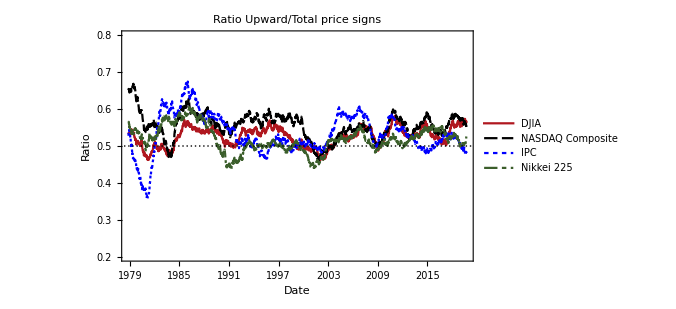

```mathematica
DateListPlot[
database[[All,"PriceChangeRatio"]],
{First[database]["FirstDate"],First[database]["LastDate"]},
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"Ratio Upward/Total price signs",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.8}}
]
```

## Samples size

```mathematica
GetInfo[market_]:=Module[{name,sampleSize,partitionSize,firstDate, lastDate},
name = market["Name"];
sampleSize = Length[market["Prices"]];
partitionSize = Length[Partition[TrendDuration[market["Prices"]],504,1]];
firstDate = DateString[market["FirstDate"],"ISODate"];
lastDate = DateString[market["LastDate"],"ISODate"];

Return[{name,sampleSize,partitionSize, firstDate,lastDate}];
];
```

```mathematica
info = Map[GetInfo,database];
Grid[Join[{{"Market name","Sample size","Partition size","First date","Last date"}},info],Background->{None,{Gray}}]
```

Market name | Sample size | Partition size | First date | Last date
DJIA | 10354 | 4830 | 1978-10-30 | 2019-09-26
NASDAQ Composite | 10317 | 4216 | 1978-10-30 | 2019-09-26
IPC | 10216 | 3901 | 1978-10-30 | 2019-09-26
Nikkei 225 | 10104 | 4584 | 1978-10-30 | 2019-09-27

## Parameter estimation

```mathematica
UpwardDatedTrendDuration[dates_,prices_] := Module[{simpleReturns,splitted,posTrends,result},
simpleReturns = DatedSimpleReturns[dates,prices];
splitted =SplitBy[MapAt[Sign,simpleReturns,{All,2}],Last];
posTrends = Select[splitted,Apply[Or,Positive[#[[All,2]]]]&];
result = Map[{#[[1,1]],Length[#]}&,posTrends];
Return[result];
];
DownwardDatedTrendDuration[dates_,prices_] := Module[{simpleReturns,splitted,negTrends,result},
simpleReturns = DatedSimpleReturns[dates,prices];
splitted =SplitBy[MapAt[Sign,simpleReturns,{All,2}],Last];
negTrends = Select[splitted,Apply[Or,Negative[#[[All,2]]]]&];
result = Map[{#[[1,1]],Length[#]}&,negTrends];
Return[result];
];

EstimatePInTime[dates_,prices_,trendDurationFunction_,window_,skip_]:=Module[{p,ps,trendDuration,part,datesPart,pricesPart,outDates},
trendDuration = trendDurationFunction[dates,prices];
part = Partition[trendDuration,window,skip];
datesPart = part[[All,All,1]];
pricesPart = part[[All,All,2]];

outDates = Map[Last,part[[All,All,1]]];
ps = Map[p/.FindDistributionParameters[#-1,GeometricDistribution[p]]&,pricesPart];

Return[Transpose[{outDates,ps}]];
];
EstimateGoodnessOfFitInTime[dates_,prices_,trendDurationFunction_,window_,skip_]:=Module[{fit,p,ps,trendDuration,part,datesPart,pricesPart,outDates},
trendDuration = trendDurationFunction[dates,prices];
part = Partition[trendDuration,window,skip];
datesPart = part[[All,All,1]];
pricesPart = part[[All,All,2]];

outDates = Map[Last,part[[All,All,1]]];
ps = Map[
(
fit = p/.FindDistributionParameters[#-1,GeometricDistribution[p]];
DistributionFitTest[#-1,GeometricDistribution[fit]]
)&,
pricesPart
];

Return[Transpose[{outDates,ps}]];
];
```

All

```mathematica
AddToDataset[database,"EstimatedPInTime",EstimatePInTime[#1,#2,DatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimateGoodnessOfFitInTime",EstimateGoodnessOfFitInTime[#1,#2,DatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

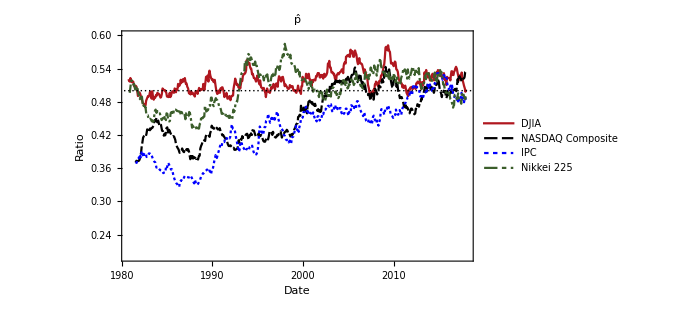

```mathematica
DateListPlot[
database[[All,"EstimatedPInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"p̂",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.6}}
]
```

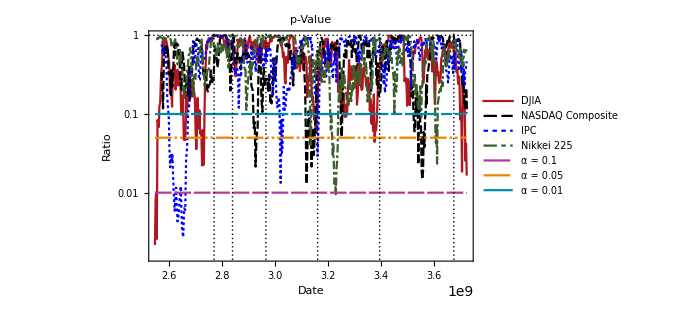

```mathematica
market = First[database];
{firstDate,lastDate} = {First[First[market["EstimateGoodnessOfFitInTime"]]],First[Last[market["EstimateGoodnessOfFitInTime"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];
plotData = Join[database[[All,"EstimateGoodnessOfFitInTime"]],uppList];

DateListLogPlot[
plotData,
PlotLegends->LineLegend[Join[database[[All,"Name"]],{"α = 0.1","α = 0.05","α = 0.01"}],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"p-Value",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.7000000000000001, 0.23, 0.59],RGBColor[0.92, 0.52, 0.],RGBColor[0., 0.55, 0.66]},
PlotMarkers->None,
Joined->True,
PlotRange->All,
GridLines->{dateObjects,{1}}
]
```

Both

```mathematica
AddToDataset[database,"EstimatedPositivePInTime",EstimatePInTime[#1,#2,UpwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimatedNegativePInTime",EstimatePInTime[#1,#2,DownwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

```mathematica
PlotEstimatedP[market_]:=DateListPlot[
{market["EstimatedPositivePInTime"],market["EstimatedNegativePInTime"]},
PlotLegends->If[market["Name"] =="DJIA",
Placed[LineLegend[{"Upward","Downward"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
None
],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{dateObjects,{0.5}},
GridLinesStyle->{Directive[Dashed],Directive[Thick]},
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0, 0, 1]},
PlotMarkers->None,
Joined->True,
PlotRange->All
];
```

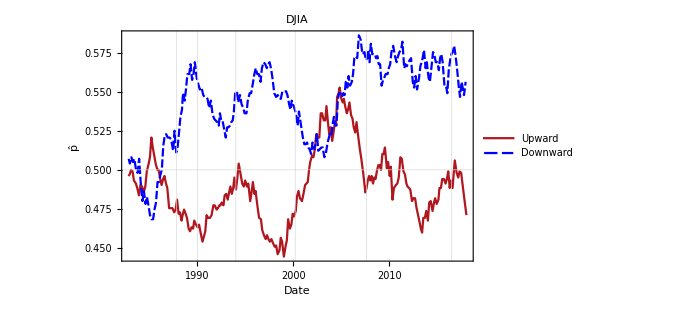
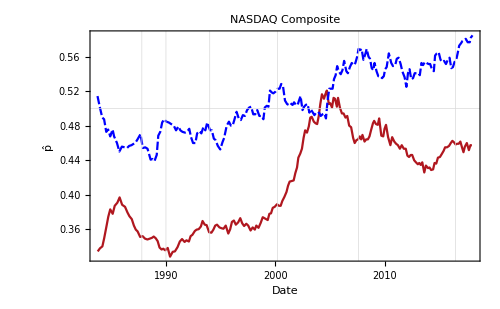
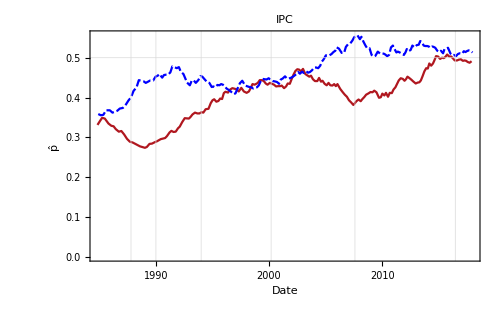
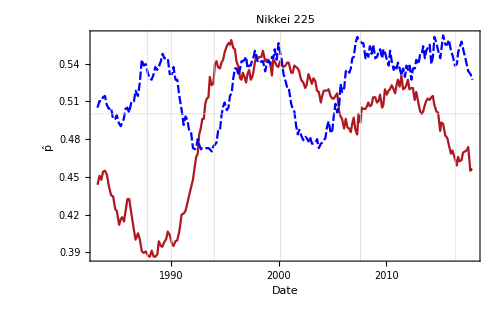

```mathematica
Map[PlotEstimatedP,database]
```

Positive

```mathematica
AddToDataset[database,"EstimatedUpwardPInTime",EstimatePInTime[#1,#2,UpwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimateUpwardGoodnessOfFitInTime",EstimateGoodnessOfFitInTime[#1,#2,UpwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

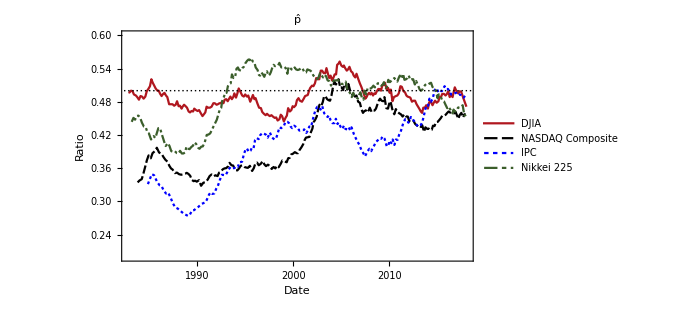

```mathematica
DateListPlot[
database[[All,"EstimatedUpwardPInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"p̂",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.6}}
]
```

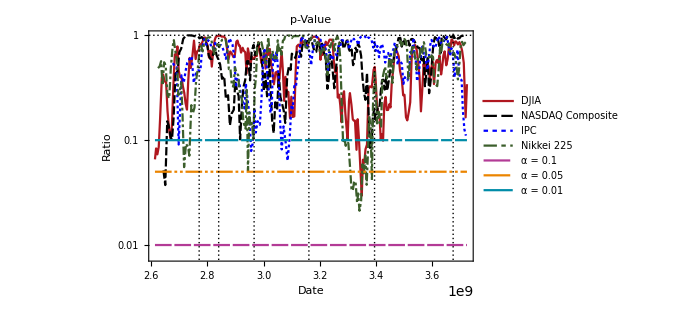

```mathematica
market = First[database];
{firstDate,lastDate} = {First[First[market["EstimateUpwardGoodnessOfFitInTime"]]],First[Last[market["EstimateUpwardGoodnessOfFitInTime"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];
plotData = Join[database[[All,"EstimateUpwardGoodnessOfFitInTime"]],uppList];

DateListLogPlot[
plotData,
PlotLegends->LineLegend[Join[database[[All,"Name"]],{"α = 0.1","α = 0.05","α = 0.01"}],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"p-Value",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.7000000000000001, 0.23, 0.59],RGBColor[0.92, 0.52, 0.],RGBColor[0., 0.55, 0.66]},
PlotMarkers->None,
Joined->True,
PlotRange->All,
GridLines->{dateObjects,{1}}
]
```

Negative

```mathematica
AddToDataset[database,"EstimatedDownwardPInTime",EstimatePInTime[#1,#2,DownwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimateDownwardGoodnessOfFitInTime",EstimateGoodnessOfFitInTime[#1,#2,DownwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

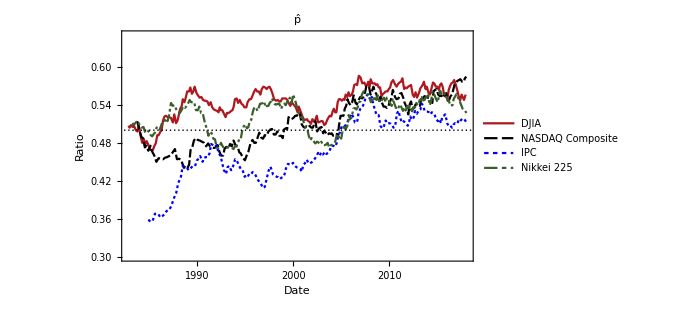

```mathematica
DateListPlot[
database[[All,"EstimatedDownwardPInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"p̂",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.3,0.65}}
]
```

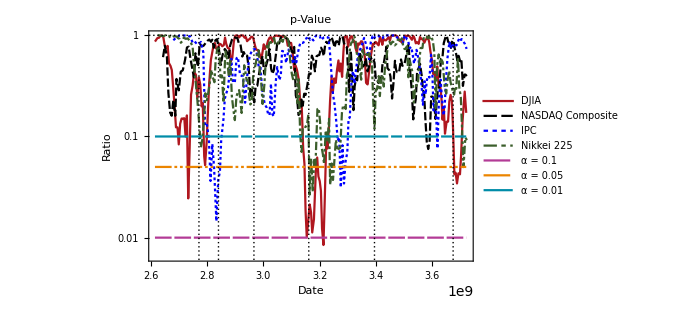

```mathematica
market = First[database];
{firstDate,lastDate} = {First[First[market["EstimateDownwardGoodnessOfFitInTime"]]],First[Last[market["EstimateDownwardGoodnessOfFitInTime"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];
plotData = Join[database[[All,"EstimateDownwardGoodnessOfFitInTime"]],uppList];

DateListLogPlot[
plotData,
PlotLegends->LineLegend[Join[database[[All,"Name"]],{"α = 0.1","α = 0.05","α = 0.01"}],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"p-Value",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.7000000000000001, 0.23, 0.59],RGBColor[0.92, 0.52, 0.],RGBColor[0., 0.55, 0.66]},
PlotMarkers->None,
Joined->True,
PlotRange->All,
GridLines->{dateObjects,{1}}
]
```

## Record statistic

```mathematica
NewRecord[lastRecord_,list_]:=SelectFirst[list,#>lastRecord&];
GetRecords[list_]:=Block[{recordCanditates,records},
recordCanditates = DeleteDuplicates[list];
records = DeleteCases[Drop[FixedPointList[NewRecord[#,recordCanditates]&,0],1],_Missing];
Return[records];
];
GetRecordTimes[list_]:=SimpleReturns[Flatten[Map[FirstPosition[list,#]&,GetRecords[list]]]];
GetWindowedRecordTimes[list_,window_]:=Flatten[Map[GetRecordTimes,Partition[list,UpTo[window]]]];
GetWindowedRecordTimes[list_,window_,skip_]:=Flatten[Map[GetRecordTimes,Partition[list,UpTo[window],skip]]];
GetNumberOfRecordBreaks[list_,window_,skip_]:=Map[Length[GetRecordTimes[#]]&,Partition[list,UpTo[window],skip]];
```

```mathematica
records = Map[GetRecordTimes[TrendDuration[#["Prices"]]]&,orderedDatabase]
```

{{1,2,11,14,3304},{1,2,9,51,52,174},{1,19,21,68,190,671},{1,2,2154}}

```mathematica
ListLinePlot[records,
PlotRange->All,
PlotLegends->Placed[LineLegend[orderedDatabase[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Time",15], Style["Record value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"Records",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.3,0.65}},
Frame->True
]
```

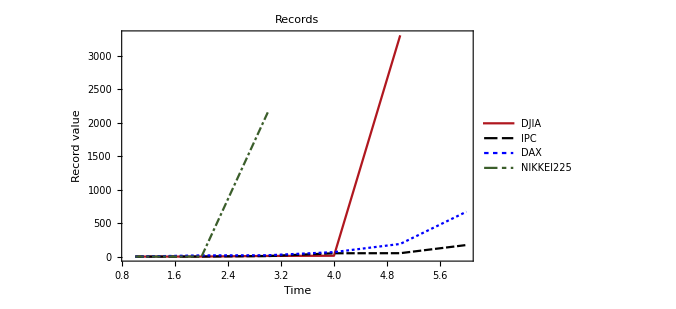
```mathematica
-Graphics-&P 500
```

```mathematica
HistogramPoints[data_]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,Automatic,"Probability"],1]];
HistogramPoints[data_,bspec_]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,bspec,"Probability"],1]];
HistogramPointPlot[data_,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
RecordTimesStatistic[market_,window_]:=Block[{prices = market["Prices"],part,result},
part = Partition[TrendDuration[prices],UpTo[window],1];
result = Flatten[Map[GetRecordTimes,part]];
Return[result];
];
RecordTimesStatisticPlot[market_,window_,scaling_ :None]:=Block[{prices = market["Prices"],fittedDist,fittedPts,data,pltData,p,model,a,k,t,fit,fittedModel},
data = RecordTimesStatistic[market,window];
pltData = Drop[HistogramPoints[data],-1];
model= k t^a;
fit = FindFit[pltData,model,{a,k},t];
fittedModel = model /.FindFit[pltData,model,{a,k},t];

fittedPts = Table[{t,fittedModel},{t,Min[data],Max[data],1}];


ListPlot[
pltData,
Joined->{False,True},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->All,
FrameLabel->{Style["Time",15], Style["Probability",15]}, 
PlotLabel->market["Name"],
ScalingFunctions->scaling,
PlotLegends->Placed[LineLegend[{"Data",Row[{"Fit: ",StandardForm[fittedModel]}]},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
]
];
```

```mathematica
First[database]["FirstDate"]
```

{1978,10,30}

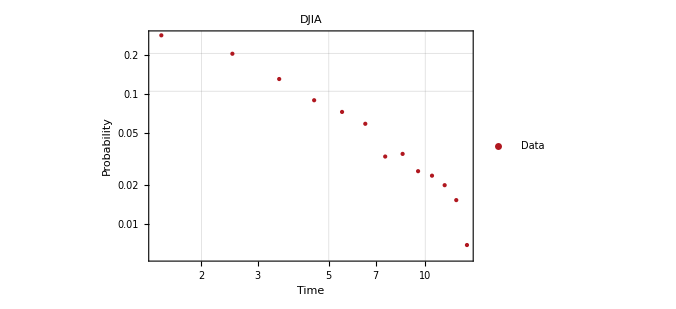
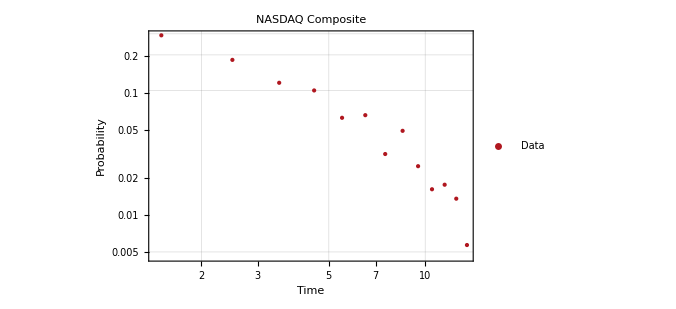
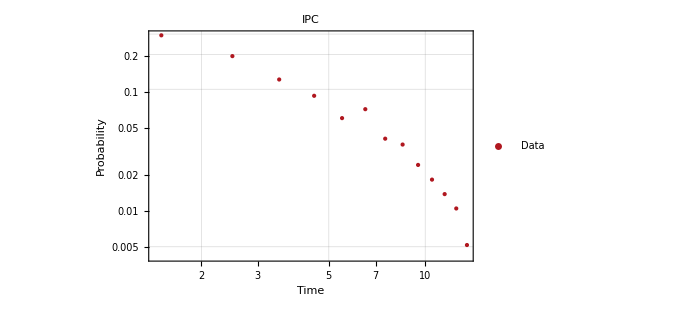
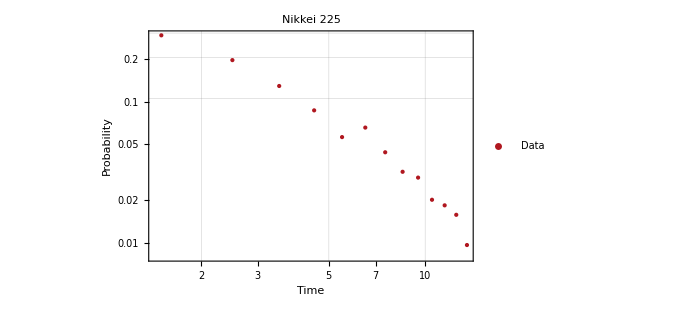

```mathematica
Map[RecordTimesStatisticPlot[#,15,{"Log","Log"}]&,database]
```

```mathematica
Map[Export[StringJoin[{NotebookDirectory[],"/",#["Name"],".csv"}],HistogramPoints[RecordTimesStatistic[#,50]]]&,database]
```

### Distribution

```mathematica
RecordTimeTestZipf[market_,window_ :50]:=Block[{prices,result,ρ,pval,param,conclusion},
prices = market["Prices"];
result = GetWindowedRecordTimes[TrendDuration[prices],window];

param = FindDistributionParameters[result,ZipfDistribution[window,ρ]];
pval = PearsonChiSquareTest[result,ZipfDistribution[window,ρ]];
conclusion = PearsonChiSquareTest[result,ZipfDistribution[window,ρ],"ShortTestConclusion"];

{market["Name"],ZipfDistribution[window,ρ] /. param,pval,conclusion}
];
```

50 day window

```mathematica
Grid[Map[RecordTimeTestZipf,orderedDatabase]]
```

DJIA | ZipfDistribution[50,0.052485] | 0.417482 | Do not reject
IPC | ZipfDistribution[50,0.0906361] | 0.4358 | Do not reject
DAX | ZipfDistribution[50,0.0987377] | 0.342806 | Do not reject
NIKKEI225 | ZipfDistribution[50,0.110174] | 0.913052 | Do not reject

100 day window

```mathematica
Grid[Map[RecordTimeTestZipf[#,100]&,orderedDatabase]]
```

DJIA | ZipfDistribution[100,0.070823] | 0.97317 | Do not reject
IPC | ZipfDistribution[100,0.0488894] | 0.666173 | Do not reject
DAX | ZipfDistribution[100,0.114262] | 0.317073 | Do not reject
NIKKEI225 | ZipfDistribution[100,0.10059] | 0.950429 | Do not reject

200 day window

```mathematica
Grid[Map[RecordTimeTestZipf[#,200]&,orderedDatabase]]
```

DJIA | ZipfDistribution[200,0.0286299] | 0.534607 | Do not reject
IPC | ZipfDistribution[200,0.0402704] | 0.884089 | Do not reject
DAX | ZipfDistribution[200,0.10421] | 0.706546 | Do not reject
NIKKEI225 | ZipfDistribution[200,0.158665] | 0.99123 | Do not reject

### Number of record breaks

```mathematica
NumberOfRecordBreaksHistogram[market_,window_,skip_]:=Block[{recordBreaks},
recordBreaks = GetNumberOfRecordBreaks[TrendDuration[market["Prices"]],window,skip];
Histogram[
recordBreaks,
Automatic,
"Probability",
PlotTheme->"Monochrome", 
FrameLabel->{Style["Number of record breaks",15], Style["Probability",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True,
Frame->True
]
];
```

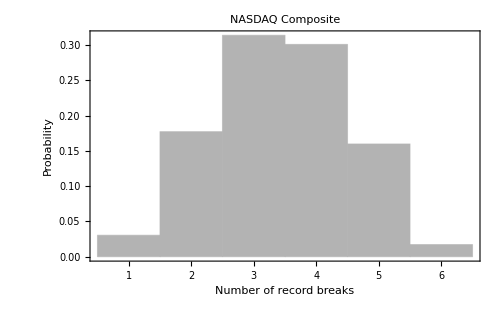
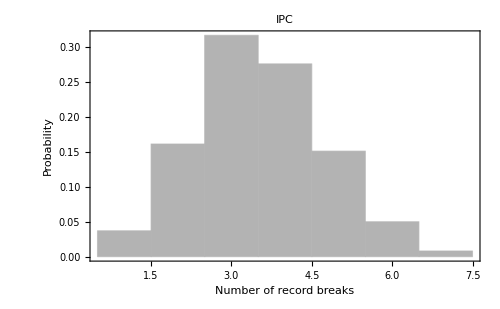
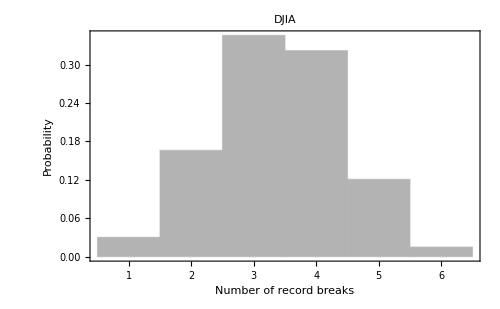
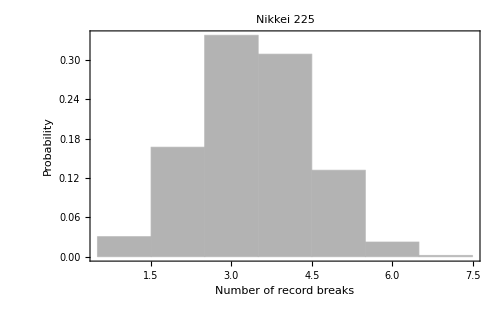

```mathematica
Map[NumberOfRecordBreaksHistogram[#,50,1]&,orderedDatabase]
```

```mathematica
DatedTrendDuration[datedPrices_]:=Block[{endpoints,datedTD},
endpoints = Map[First, TakeList[datedPrices, Append[TrendDuration[datedPrices[[All, 2]]], All]]];
datedTD = Transpose[{Drop[endpoints[[All, 1]],-1], TrendDuration[datedPrices[[All, 2]]]}];
Return[datedTD];
];
DatedPrices[market_]:=Thread[{market["Dates"],market["Prices"]}];
DatedNumberOfRecordBreaks[datedPrices_List, window_ :50, skip_ :1]:=Block[{dtd},
dtd = DatedTrendDuration[datedPrices];
Thread[{dtd[[All,1]],GetNumberOfRecordBreaks[dtd[[All,2]],window,skip]}]
];
DatedNumberOfRecordBreaks[market_Association, window_ :50, skip_ :1]:=Block[{datedPrices,dtd},
datedPrices = DatedPrices[market];
dtd = DatedTrendDuration[datedPrices];
Thread[{dtd[[All,1]],GetNumberOfRecordBreaks[dtd[[All,2]],window,skip]}]
];
DatedNumberOfRecordBreaksPlot[market_, window_ :50, skip_ :1]:=DateListPlot[
DatedNumberOfRecordBreaks[market, window, skip],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Record Breaks",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotStyle->First[colors],
PlotMarkers->None,
Joined->True,
PlotLabel->market["Name"],
InterpolationOrder->0
];
```

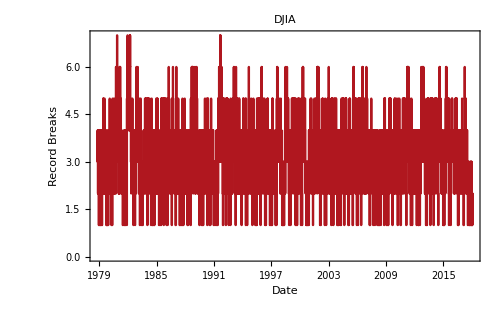
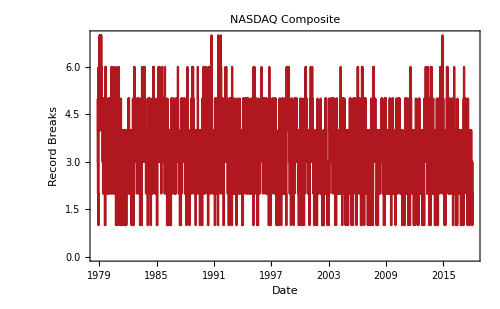
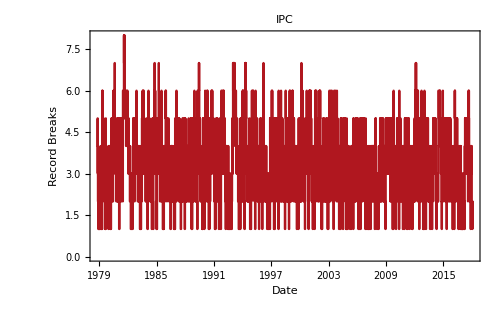
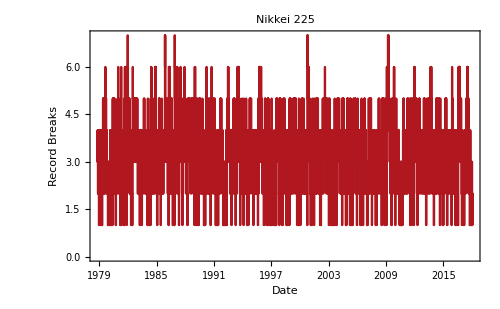

```mathematica
Map[DatedNumberOfRecordBreaksPlot,database]
```

# Waiting time analysis

We can model waiting times as the number of failures (days without observing the desired trend duration) in a sequence of trials (days passed) with probability of sucess p. This is also a geometric distribution.

Distribution

Smooth histogram

```mathematica
DayLegends[n_Integer]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
Range[n]
];
DayLegends[l_List]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
l
];

WaitTime[prices_,duration_]:=Block[{td,grouped,dayIntervals},
td = TrendDuration[prices];
grouped = Drop[Split[td,#≠duration&],1];
dayIntervals = Map[Length,grouped]-1;
Return[dayIntervals];
];
WaitTimeForRuns[prices_,range_:4]:=Map[WaitTime[prices,#]&,Range[range]];

WaitTimeForMarket[market_]:=Block[{dist},
dist =WaitTimeForRuns[market["Prices"]];
SmoothHistogram[dist,1,
PlotRange->{{0,50},All},
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait",bigFontSize],Style["PDF",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]
];
```

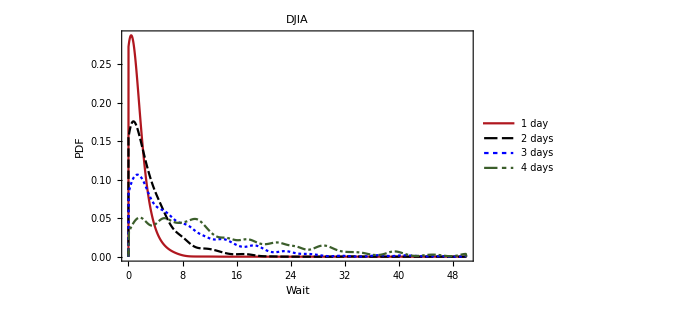
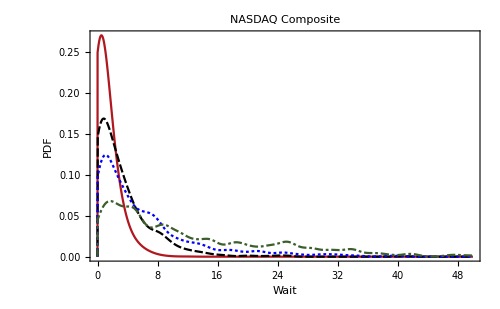
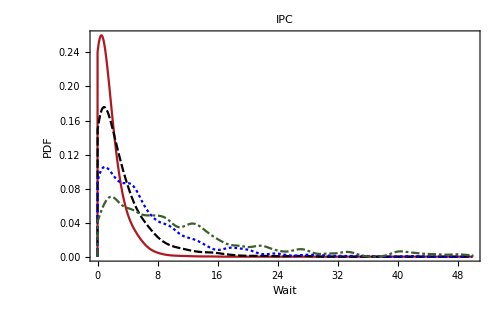
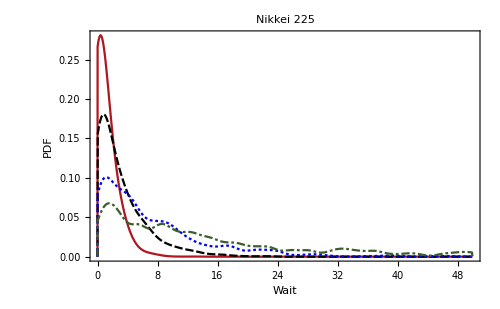

```mathematica
Map[WaitTimeForMarket,database]
```

Discrete

```mathematica
HistogramPoints[data_]:=SortBy[Map[{#,N@(Count[data,#]/Length[data])}&,DeleteDuplicates[data]],First];
GenerateFitted[p_,max_]:=Table[{k,PDF[GeometricDistribution[p],k]},{k,0,max}];
DiscreteHistogramWaitTime[market_]:=Block[{waitTimes,histogramPts,ps,legend,fitted},
waitTimes = WaitTimeForRuns[market["Prices"]];
histogramPts = Map[HistogramPoints,waitTimes];
ps = Map[EstimateP,waitTimes];
legend = MapThread[StringJoin[#1,", p̂ = ",ToString[#2]]&,{DayLegends[4],ps}];
fitted = Map[GenerateFitted[#,70]&,ps];

ListLogPlot[
Join[fitted,histogramPts],
Joined->{True,True,True,True,False,False,False,False},
PlotRange->{{0,70},{10^-5,1}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait time (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
ImageSize->600,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[legend,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
]
];
```

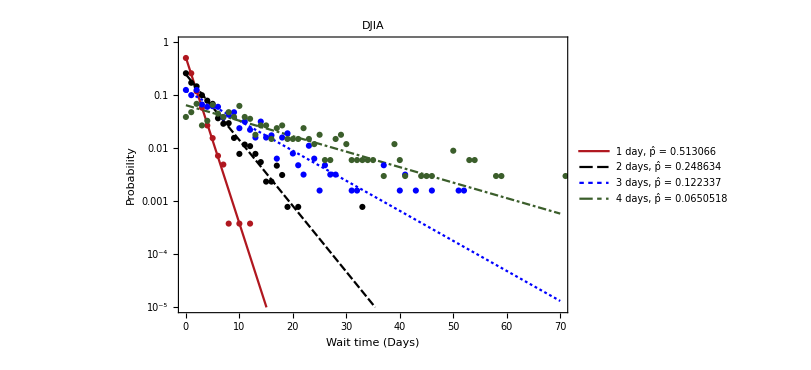
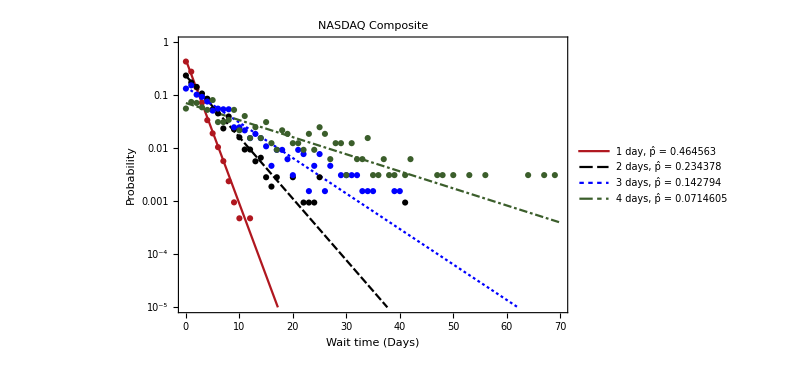
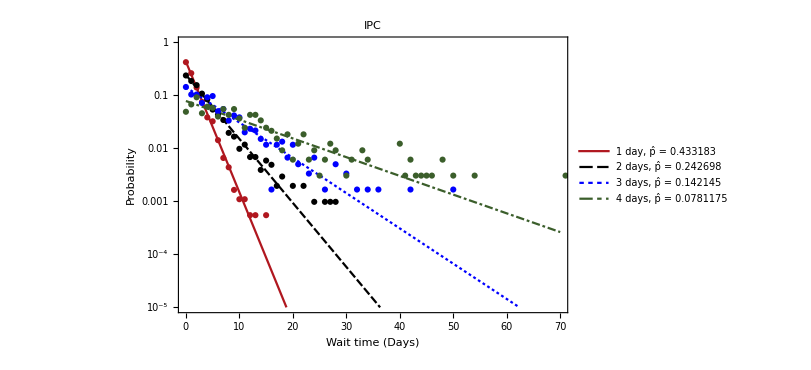
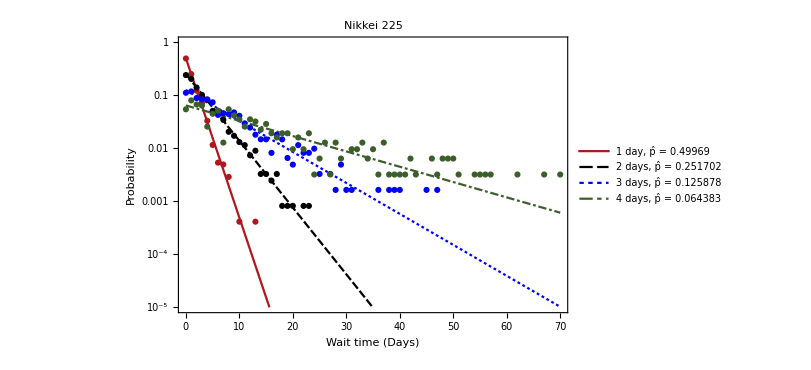

```mathematica
Map[DiscreteHistogramWaitTime,database]
```

Find fit automatically

```mathematica
FindWaitTimeDistributions[market_]:=Map[FindDistribution[WaitTime[market,#]]&,Range[4]];
FormatFindWaitTimeDist[market_]:=Labeled[Grid[Thread[{Range[4],FindWaitTimeDistributions[market]}]],market["Name"],Top];
Map[FormatFindWaitTimeDist,database]
```

{1 | GeometricDistribution[0.513066]
2 | GeometricDistribution[0.248634]
3 | GeometricDistribution[0.122337]
4 | GeometricDistribution[0.0650518]DJIA,1 | GeometricDistribution[0.464563]
2 | GeometricDistribution[0.234378]
3 | GeometricDistribution[0.142794]
4 | GeometricDistribution[0.0714605]NASDAQ Composite,1 | GeometricDistribution[0.433183]
2 | GeometricDistribution[0.242698]
3 | GeometricDistribution[0.142145]
4 | GeometricDistribution[0.0781175]IPC,1 | GeometricDistribution[0.49969]
2 | GeometricDistribution[0.251702]
3 | GeometricDistribution[0.125878]
4 | GeometricDistribution[0.064383]Nikkei 225}

Test for a geometric distribution

```mathematica
WaitTimeGOF[market_]:=Block[{dist,testData},
dist = Map[WaitTime[market,#]&,Range[4]];
testData = MapThread[{GeometricDistribution[#2],PearsonChiSquareTest[#1,GeometricDistribution[#2]]}&,{dist,{0.5,0.25,0.125,0.0625}}];

Labeled[
Grid[
Prepend[testData,{"Hypothesis","p-value"}],
Dividers->{{False,True},{False,True}}
],
market["Name"],
Top
]
];
```

```mathematica
Map[WaitTimeGOF,database]
```

{Hypothesis | p-value
GeometricDistribution[0.5] | 0.517962
GeometricDistribution[0.25] | 0.507141
GeometricDistribution[0.125] | 0.429097
GeometricDistribution[0.0625] | 0.192288DJIA,Hypothesis | p-value
GeometricDistribution[0.5] | 7.19167×10^-7
GeometricDistribution[0.25] | 0.0854396
GeometricDistribution[0.125] | 0.0101065
GeometricDistribution[0.0625] | 0.122488NASDAQ Composite,Hypothesis | p-value
GeometricDistribution[0.5] | 6.41239×10^-18
GeometricDistribution[0.25] | 0.524296
GeometricDistribution[0.125] | 0.00792484
GeometricDistribution[0.0625] | 0.00493737IPC,Hypothesis | p-value
GeometricDistribution[0.5] | 0.364495
GeometricDistribution[0.25] | 0.843388
GeometricDistribution[0.125] | 0.575041
GeometricDistribution[0.0625] | 0.403271Nikkei 225}

In time

```mathematica
RunDistributionInTime[market_,window_,skip_]:=DynamicModule[{part,hs},
part = Partition[market["Prices"],window,skip];
hs = Map[
SmoothHistogram[
WaitTimeForRuns[#,3],1,
PlotRange->{{0,50},{0,0.30}},
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait",bigFontSize],Style["PDF",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[3],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]&,
part
];

Manipulate[hs[[i]],{i,1,Length[hs],1}]
];

GeneratePointsAndFit[prices_]:=Block[{waitTimes,histogramPts,ps,legend,fitted},
waitTimes = WaitTimeForRuns[prices];
histogramPts = Map[HistogramPoints,waitTimes];
ps = Map[EstimateP,waitTimes];
legend = MapThread[StringJoin[#1,", p̂ = ",ToString[#2]]&,{DayLegends[4],ps}];
fitted = Map[GenerateFitted[#,70]&,ps];

{Join[fitted,histogramPts],legend}
];
DiscreteHistogramWaitTimeEvolution[market_,window_,skip_]:=DynamicModule[{part,legend,data,hs},
part = Partition[market["Prices"],window,skip];

hs = Map[
({data,legend} = GeneratePointsAndFit[#];
ListLogPlot[
data,
Joined->{True,True,True,True,False,False,False,False},
PlotRange->{{0,70},{10^-15,1}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait time (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
ImageSize->600,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[legend,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
])&,
part
];

Manipulate[hs[[i]],{i,1,Length[hs],1},SaveDefinitions->True]
];
```

```mathematica
Map[DiscreteHistogramWaitTimeEvolution[#,2000,200]&,database]
```

{,,,}

### More detailed view

```mathematica
GeneratePointsAndFit2[prices_]:=Block[{waitTimes,histogramPts,p,legend,fitted},
waitTimes = WaitTime[prices,1];
histogramPts = HistogramPoints[waitTimes];
p = EstimateP[waitTimes];
legend = StringJoin["p̂ = ",ToString[p]];
fitted = GenerateFitted[p,70];

{{histogramPts,fitted},legend}
];
DiscreteHistogramWaitTimeEvolution2[market_,window_,skip_]:=DynamicModule[{part,ref,legend,data,hs},
part = Partition[market["Prices"],window,skip];
ref = GenerateFitted[0.5,16];

hs = Map[
({data,legend} = GeneratePointsAndFit2[#];
ListLogPlot[
Join[data,{ref}],
Joined->{False,True,True},
PlotRange->{{0,16},{10^-7,1}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait time (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0]},
ImageSize->600,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[{"Data","Fit: "<>legend,"p̂ = 0.5"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
])&,
part
];

Manipulate[hs[[i]],{i,1,Length[hs],1}]
]
```

```mathematica
Map[DiscreteHistogramWaitTimeEvolution2[#,2000,200]&,database]
```

Observación: Tanto el IPC como NASDAQ presentan periodos en los que transcurre una cantidad de días hasta que se vuelve a presentar un run de 1 día que es mayor que la esperada asumiendo la hipótesis nula de caminata aleatoria.

Estimate in time

```mathematica
EstimatePRunsEvolution[market_,duration_,window_,skip_]:=Block[{part,datesPart,hs,p},
part = Partition[market["Prices"],window,skip];
datesPart = Partition[market["Dates"],window,skip];
hs = Map[WaitTime[#,duration]&,part];

MapThread[{Last[#1],p/.FindDistributionParameters[#2,GeometricDistribution[p]]}&,{datesPart,hs}]
];
PlotPRunsEvolution[market_,window_,skip_]:=Block[{ps},
ps = Map[EstimatePRunsEvolution[market,#,window,skip]&,Range[3]];
DateListPlot[ps,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5,0.25,0.125}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotLabel->market["Name"],
PlotLegends->If[market["Name"]=="DJIA",Placed[LineLegend[DayLegends[3],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}],None]
]
];
```

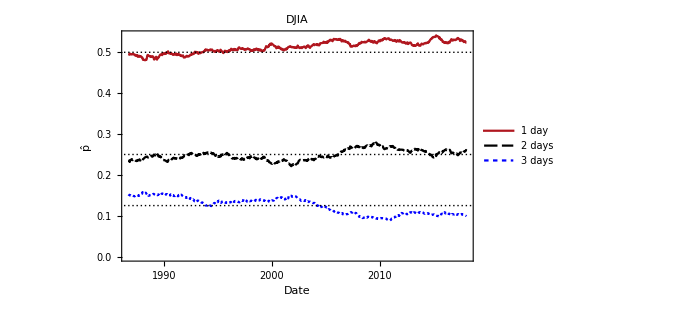
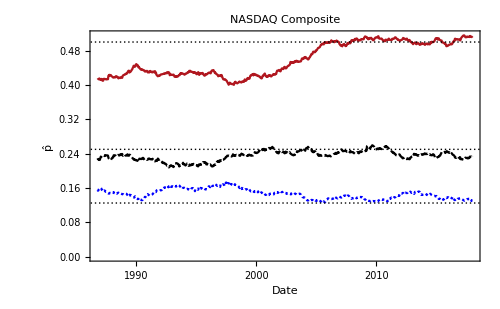
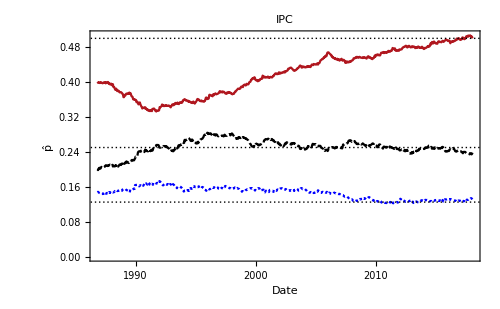
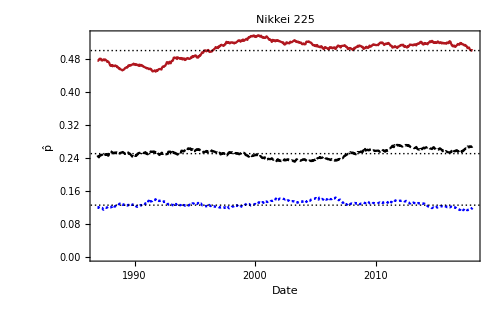

```mathematica
Map[PlotPRunsEvolution[#,2000,10]&,database]
```

One day trends are possibly the cause of deviations from the random walk.

Test in time

```mathematica
HypothesisGOF[wt_]:=MapThread[PearsonChiSquareTest[#1,GeometricDistribution[#2]]&,{wt,{0.5,0.25,0.125}}];
RunDistributionHypothesisGOFInTime[market_,window_,skip_]:=Block[{part,hs,pvalues},
part = Partition[market["Prices"],window,skip];
hs = Map[WaitTimeForRuns[#,3]&,part];
pvalues = Transpose[Map[HypothesisGOF,hs]];

DateListLogPlot[
pvalues,
{market["Dates"][[2000]],market["Dates"][[-1]]},
PlotLegends->If[market["Name"]=="DJIA",Placed[LineLegend[DayLegends[3],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],None],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p-Value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0,1}},
Frame->True,
PlotLabel->market["Name"],
GridLines->{{},{0.01,0.05,0.1}}
]
];
```

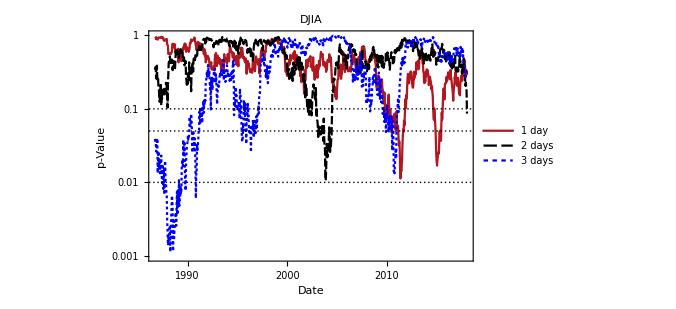
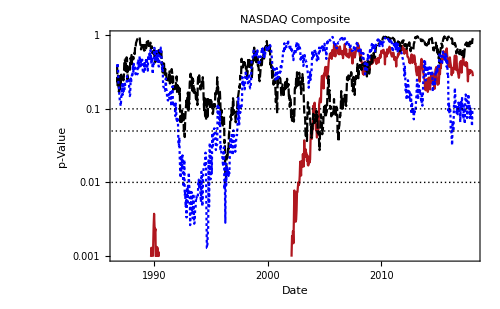
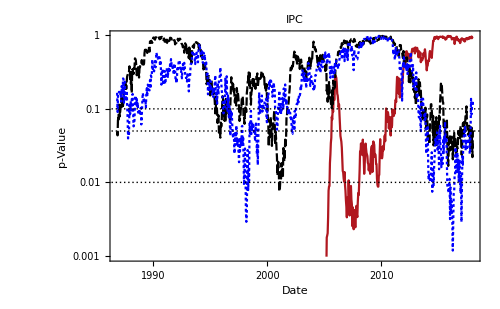
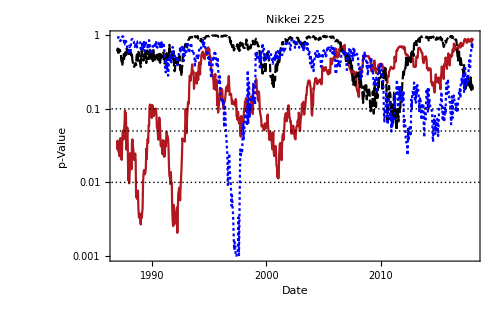

```mathematica
Map[RunDistributionHypothesisGOFInTime[#,2000,10]&,database]
```

Directional wait time estimation

```mathematica
SignedTrendDuration[prices_] := Map[First[#]*Length[#]&, Split[Sign[Returns[prices]]]];
UpwardWaitTime[prices_,duration_]:=Block[{td,grouped,dayIntervals},
td = SignedTrendDuration[prices];
grouped = Drop[Split[td,#≠duration&],1];
dayIntervals = Map[Length,grouped]-1;
Return[dayIntervals];
];
DownwardWaitTime[prices_,duration_]:=Block[{td,grouped,dayIntervals},
td =SignedTrendDuration[prices];
grouped = Drop[Split[td,#≠(-duration)&],1];
dayIntervals = Map[Length,grouped]-1;
Return[dayIntervals];
];
WaitTime[prices_,duration_,"Upward"]:=UpwardWaitTime[prices,duration];
WaitTime[prices_,duration_,"Downward"]:=DownwardWaitTime[prices,duration];

EstimatePRunsEvolutionDirectional[market_,window_,skip_,direction_,duration_ :1]:=Block[{part,datesPart,hs,p},
part = Partition[market["Prices"],window,skip];
datesPart = Partition[market["Dates"],window,skip];
hs = Map[WaitTime[#,duration,direction]&,part];

MapThread[{Last[#1],p/.FindDistributionParameters[#2,GeometricDistribution[p]]}&,{datesPart,hs}]
];
PlotPRunsEvolutionDirectional[market_,window_,skip_,duration_ :1]:=Block[{pUpward,pDownward},
pUpward = EstimatePRunsEvolutionDirectional[market,window,skip,"Upward",duration];
pDownward = EstimatePRunsEvolutionDirectional[market,window,skip,"Downward",duration];

DateListPlot[{pUpward,pDownward},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{dateObjects,{0.5,0.25,0.125,0.0625}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotLabel->market["Name"],
PlotLegends->Placed[LineLegend[{"Upward","Downward"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}],
PlotRange->{Automatic,{0,0.5}}
]
];
```

### 1 day

Nota: Hay correlación entre la estimación p de los tiempos de espera de 1 día con la duración de los trends.

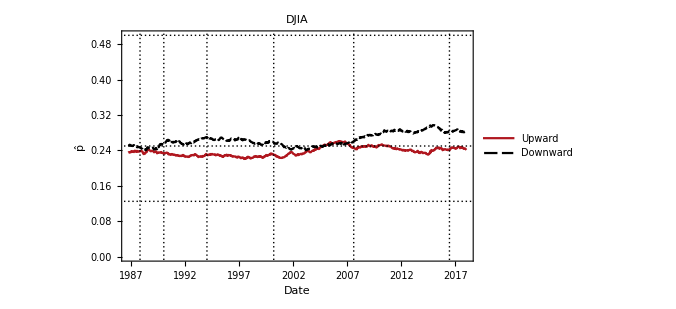
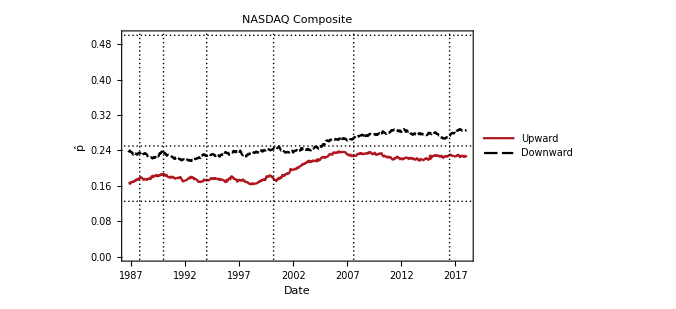
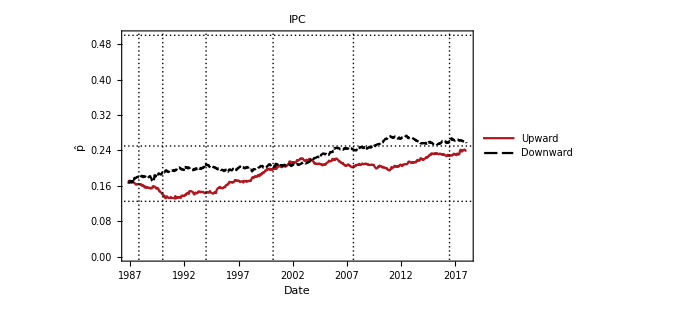
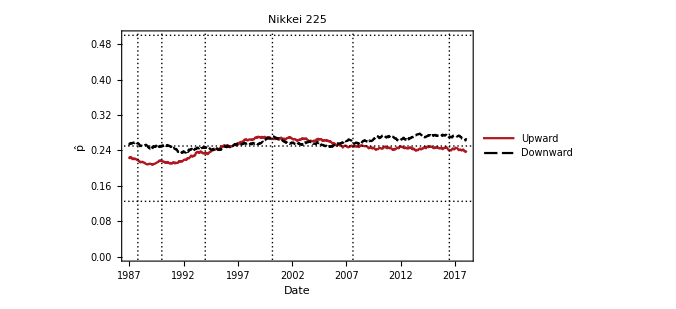

```mathematica
Map[PlotPRunsEvolutionDirectional[#,2000,10,1]&,database]
```

### 2 days

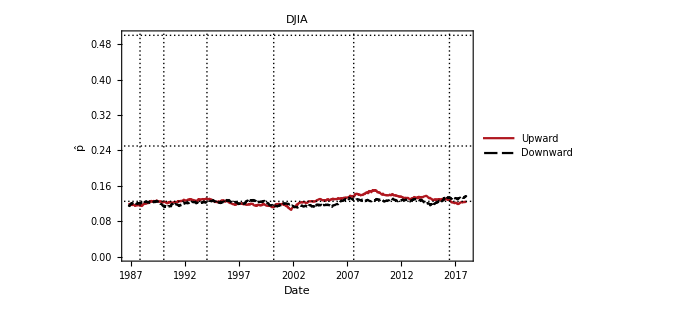
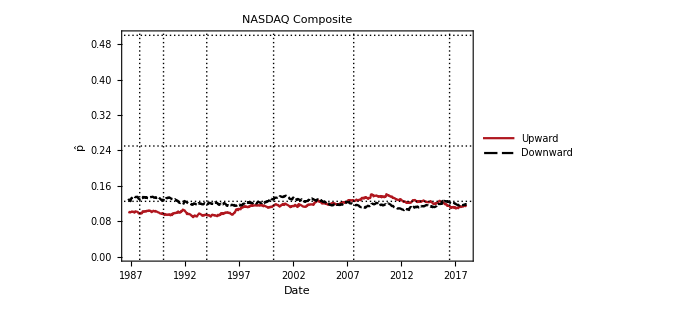
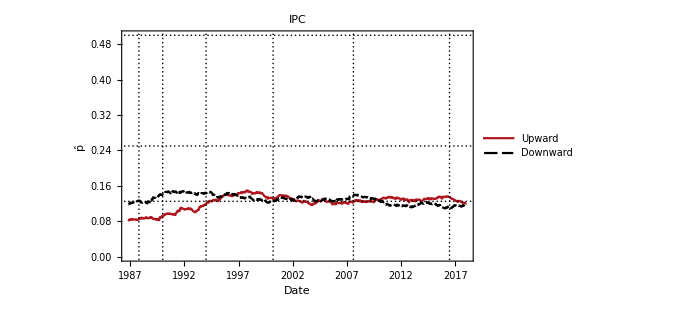
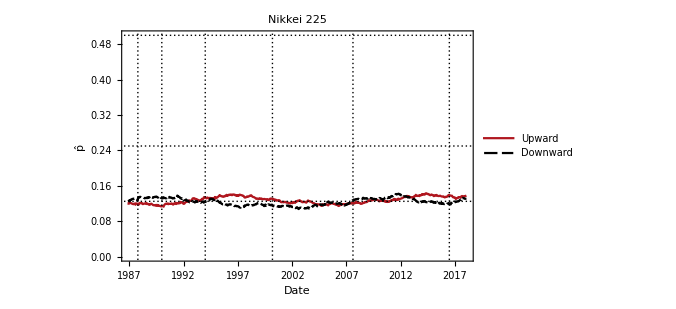

```mathematica
Map[PlotPRunsEvolutionDirectional[#,2000,10,2]&,database]
```

### 3 days

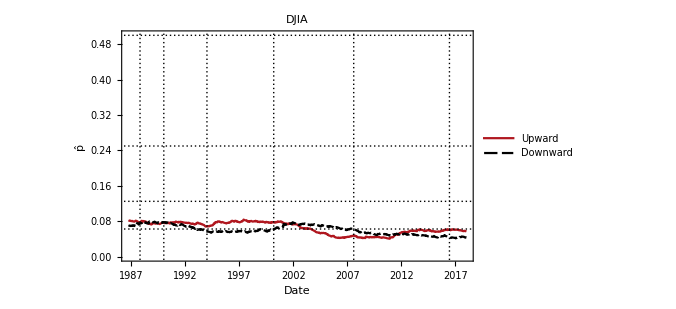
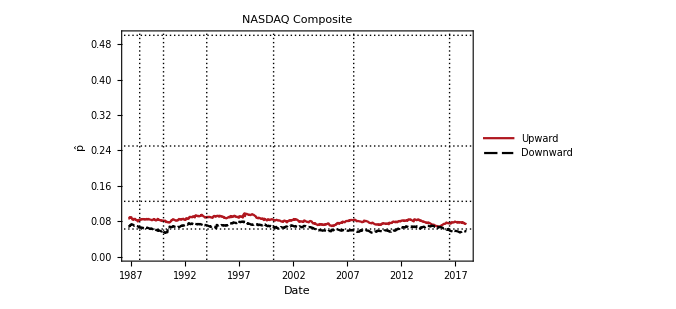
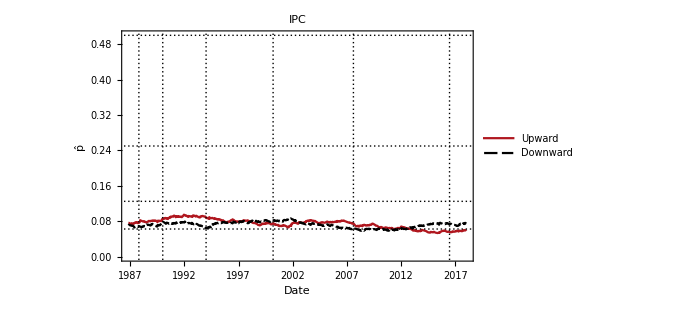
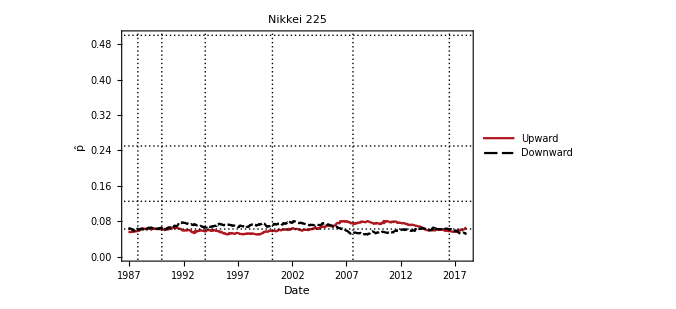

```mathematica
Map[PlotPRunsEvolutionDirectional[#,2000,10,3]&,database]
```

## Record breaking statistic

```mathematica
PlotRecordStatisticForWT[market_]:=Block[{waitTimeRecords},
waitTimeRecords = Map[GetRecordTimes,WaitTimeForRuns[market["Prices"]]];

ListLinePlot[waitTimeRecords,
PlotRange->All,
PlotLegends->Placed[LineLegend[DayLegends[4],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Time",15], Style["Record value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->market["Name"],
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.3,0.65}},
Frame->True,
PlotMarkers->{Automatic, 10}
]
];
```

```mathematica
RecordStatisticTestForWT[market_,window_ :50]:=Block[{ρ,waitingTimeRecords,results,txtresults,param,grid},
waitingTimeRecords = Map[GetWindowedRecordTimes[#,window]&,WaitTimeForRuns[market["Prices"],3]];
results = Map[PearsonChiSquareTest[#,ZipfDistribution[window,ρ]]&,waitingTimeRecords];
txtresults = Map[PearsonChiSquareTest[#,ZipfDistribution[window,ρ],"ShortTestConclusion"]&,waitingTimeRecords];
param = Map[ZipfDistribution[window,ρ]/.FindDistributionParameters[#,ZipfDistribution[window,ρ]]&,waitingTimeRecords];

grid = Grid[Prepend[Thread[{DayLegends[3],param,results,txtresults}],{"Length","Distribution","p-value","Result"}],Frame->True];
Labeled[grid,market["Name"],Top]
];

HistogramPointPlotForWT[{data1_,data2_,data3_},opts: OptionsPattern[]]:=Block[
{
pltData1 = HistogramPoints[data1], 
pltData2 = HistogramPoints[data2],
pltData3 = HistogramPoints[data3]
},

ListPlot[
{pltData1,pltData1,pltData2,pltData2,pltData3,pltData3},
Joined->{False,True,False,True,False,True},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{colors[[1]],{PointSize[Large],colors[[1]]},colors[[2]],{PointSize[Large],colors[[2]]},colors[[3]],{PointSize[Large],colors[[3]]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[Flatten[Thread[{DayLegends[3],DayLegends[3]}]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}],
FilterRules[{opts},Options[ListPlot]]
]
];
HistogramPointPlotForWT[market_,opts: OptionsPattern[]]:=Block[{data},
data = Map[GetWindowedRecordTimes[#,10,1]&,WaitTimeForRuns[market["Prices"],3]];
HistogramPointPlotForWT[data,PlotLabel->market["Name"],ScalingFunctions->"Log",PlotRange->All,opts]
];
```

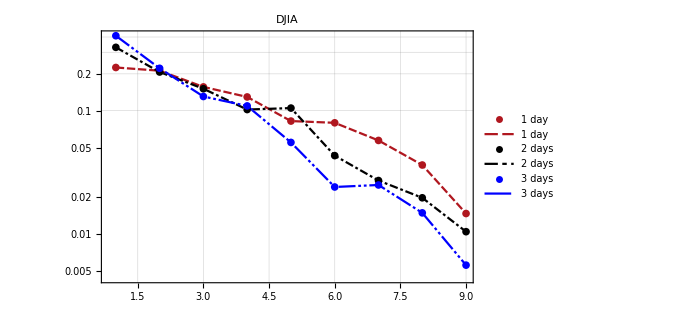
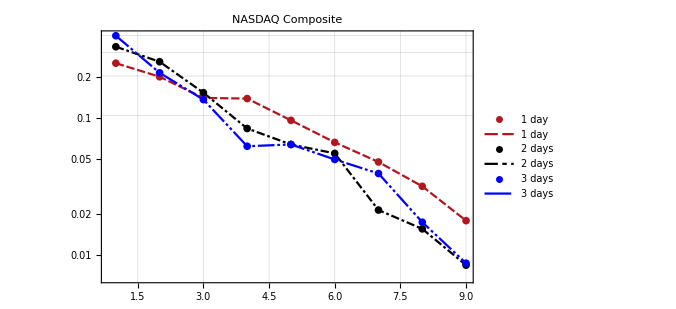
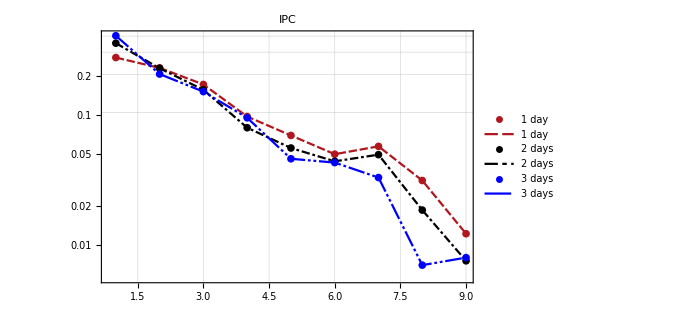
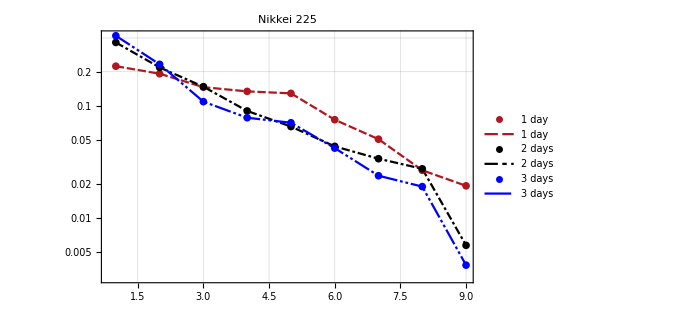

```mathematica
Map[HistogramPointPlotForWT,database]
```